# All 605 of them

## This is NOT a standalone notebook

## Normal Form

```mathematica
Clear[α,β,a1,a2,a3,yHat2,yHat1,yHat0,yHat]
Clear[γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]
Clear[γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]

yHat2List={(*1*)0.2,(*2*)0.63,(*3*)1.05,(*4*)1.14,(*5*)1.62,(*6*)2.25,(*7*)2.73,(*8*)3.39,(*9*)3.93,(*10*)4.38,(*11*)4.80};
yHat1List={(*1*)0.69,(*2*)0.99,(*3*)1.65,(*4*)1.95,(*5*)2.13,(*6*)2.55,(*7*)3.06,(*8*)3.12,(*9*)3.42,(*10*)4.23,(*11*)4.35};
yHat0List={(*1*)0.87,(*2*)1.89,(*3*)2.97,(*4*)4.17,(*5*)4.26};


plotplotlist={};
For[z=1,z<=Length[yHat1List],z++,
For[x=1,x<=Length[yHat0List],x++,
For[m=1,m<=Length[yHat2List],m++,
yHat2=yHat2List[[m]];
yHat1=yHat1List[[z]];
yHat0=yHat0List[[x]];

γ22=γ22/.{bdCoeffs2[[3]]/.interiorCoeffs};
γ20=1/γ22*(γ20/.{bdCoeffs2[[1]]/.(Join[interiorCoeffs,{yHat->yHat2}])})/.{yHat->yHat2};
γ21=1/γ22*(γ21/.{bdCoeffs2[[2]]/.(Join[interiorCoeffs,{yHat->yHat2}])})/.{yHat->yHat2};
γ23=1/γ22*(γ23/.{bdCoeffs2[[4]]/.(Join[interiorCoeffs,{yHat->yHat2}])})/.{yHat->yHat2};
γ24=1/γ22*(γ24/.{bdCoeffs2[[5]]/.(Join[interiorCoeffs,{yHat->yHat2}])})/.{yHat->yHat2};
a20=1/γ22*(a20/.{bdCoeffs2[[6]]/.(Join[interiorCoeffs,{yHat->yHat2}])})/.{yHat->yHat2};
a21=1/γ22*(a21/.{bdCoeffs2[[7]]/.(Join[interiorCoeffs,{yHat->yHat2}])})/.{yHat->yHat2};
a22=1/γ22*(a22/.{bdCoeffs2[[8]]/.(Join[interiorCoeffs,{yHat->yHat2}])})/.{yHat->yHat2};
a23=1/γ22*(a23/.{bdCoeffs2[[9]]/.(Join[interiorCoeffs,{yHat->yHat2}])})/.{yHat->yHat2};
a24=1/γ22*(a24/.{bdCoeffs2[[10]]/.(Join[interiorCoeffs,{yHat->yHat2}])})/.{yHat->yHat2};
a25=1/γ22*(a25/.{bdCoeffs2[[11]]/.(Join[interiorCoeffs,{yHat->yHat2}])})/.{yHat->yHat2};
a26=1/γ22*(a26/.{bdCoeffs2[[12]]/.(Join[interiorCoeffs,{yHat->yHat2}])})/.{yHat->yHat2};
γ22=γ22/γ22/.{yHat->yHat2};



γ11=γ11/.{bdCoeffs1[[2]]/.interiorCoeffs};
γ10=1/γ11*(γ10/.{bdCoeffs1[[1]]/.(Join[interiorCoeffs,{yHat->yHat1}])})/.{yHat->yHat1};
γ12=1/γ11*(γ12/.{bdCoeffs1[[3]]/.(Join[interiorCoeffs,{yHat->yHat1}])})/.{yHat->yHat1};
γ13=1/γ11*(γ13/.{bdCoeffs1[[4]]/.(Join[interiorCoeffs,{yHat->yHat1}])})/.{yHat->yHat1};
a10=1/γ11*(a10/.{bdCoeffs1[[5]]/.(Join[interiorCoeffs,{yHat->yHat1}])})/.{yHat->yHat1};
a11=1/γ11*(a11/.{bdCoeffs1[[6]]/.(Join[interiorCoeffs,{yHat->yHat1}])})/.{yHat->yHat1};
a12=1/γ11*(a12/.{bdCoeffs1[[7]]/.(Join[interiorCoeffs,{yHat->yHat1}])})/.{yHat->yHat1};
a13=1/γ11*(a13/.{bdCoeffs1[[8]]/.(Join[interiorCoeffs,{yHat->yHat1}])})/.{yHat->yHat1};
a14=1/γ11*(a14/.{bdCoeffs1[[9]]/.(Join[interiorCoeffs,{yHat->yHat1}])})/.{yHat->yHat1};
a15=1/γ11*(a15/.{bdCoeffs1[[10]]/.(Join[interiorCoeffs,{yHat->yHat1}])})/.{yHat->yHat1};
a16=1/γ11*(a16/.{bdCoeffs1[[11]]/.(Join[interiorCoeffs,{yHat->yHat1}])})/.{yHat->yHat1};
γ11=γ11/γ11/.{yHat->yHat1};



γ00=γ00/.{bdCoeffs0[[1]]/.interiorCoeffs};
γ01=1/γ00*(γ01/.{bdCoeffs0[[2]]/.(Join[interiorCoeffs,{yHat->yHat0}])})/.{yHat->yHat0};
γ02=1/γ00*(γ02/.{bdCoeffs0[[3]]/.(Join[interiorCoeffs,{yHat->yHat0}])})/.{yHat->yHat0};
a00=1/γ00*(a00/.{bdCoeffs0[[4]]/.(Join[interiorCoeffs,{yHat->yHat0}])})/.{yHat->yHat0};
a01=1/γ00*(a01/.{bdCoeffs0[[5]]/.(Join[interiorCoeffs,{yHat->yHat0}])})/.{yHat->yHat0};
a02=1/γ00*(a02/.{bdCoeffs0[[6]]/.(Join[interiorCoeffs,{yHat->yHat0}])})/.{yHat->yHat0};
a03=1/γ00*(a03/.{bdCoeffs0[[7]]/.(Join[interiorCoeffs,{yHat->yHat0}])})/.{yHat->yHat0};
a04=1/γ00*(a04/.{bdCoeffs0[[8]]/.(Join[interiorCoeffs,{yHat->yHat0}])})/.{yHat->yHat0};
a05=1/γ00*(a05/.{bdCoeffs0[[9]]/.(Join[interiorCoeffs,{yHat->yHat0}])})/.{yHat->yHat0};
a06=1/γ00*(a06/.{bdCoeffs0[[10]]/.(Join[interiorCoeffs,{yHat->yHat0}])})/.{yHat->yHat0};
γ00=γ00/γ00/.{yHat->yHat0};

interior={α->0.5770460201292381,β->0.08900836845092142,a->0.6517078440898839,b->0.24815882627035918,c->0.006009630649852392};
boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};
coeff=Flatten[Join[interior,boundary]];

LHSBorders={
{1,α12,β12},
{α21,1,α22,β22},
{β31,α31,1,α32,β32}
};
RHSBorders={
{a1,b1,c1,d1,e1,f1,g1},
{a2,b2,c2,d2,e2,f2,g2},
{a3,b3,c3,d3,e3,f3,g3}
};

LHSMatrix[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{1,1}]->1,
Band[{2,1}]->α,
Band[{1,2}]->α,
Band[{3,1}]->β,
Band[{1,3}]->β
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[LHSBorders[[i]]],j++,
M[[i,j]]=LHSBorders[[i,j]]/.coeff;
M[[n-i+1,n-j+1]]=LHSBorders[[i,j]]/.coeff
]
];

M
];

RHSMatrix[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{2,1}]->-a,
Band[{3,1}]->-b,
Band[{4,1}]->-c,
Band[{1,2}]->a,
Band[{1,3}]->b,
Band[{1,4}]->c
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[RHSBorders[[i]]],j++,
M[[i,j]]=RHSBorders[[i,j]]/.coeff;
M[[n-i+1,n-j+1]]=-RHSBorders[[i,j]]/.coeff
]
];

M
];

n=160;
LHS=LHSMatrix[n,3,coeff];
RHS=RHSMatrix[n,3,coeff];

For[j=1,j<=n,j++,LHS[[1,j]]=0];
For[j=1,j<=n,j++,LHS[[j,1]]=0];
For[j=1,j<=n,j++,RHS[[1,j]]=0];
For[j=1,j<=n,j++,RHS[[j,1]]=0];
LHS[[1,1]]=1;
LHS//MatrixForm;
RHS//MatrixForm;

mat=Inverse[LHS].RHS;
eigs=Eigenvalues[mat];
AppendTo[plotplotlist,ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[160]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,yHat2/5]]]
]
]
];
```

## Table and Color Form

```mathematica
Clear[α,β,a1,a2,a3,yHat2,yHat1,yHat0,yHat]
Clear[γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]
Clear[γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]

yHat2List={(*1*)0.2,(*2*)0.63,(*3*)1.05,(*4*)1.14,(*5*)1.62,(*6*)2.25,(*7*)2.73,(*8*)3.39,(*9*)3.93,(*10*)4.38,(*11*)4.80};
yHat1List={(*1*)0.69,(*2*)0.99,(*3*)1.65,(*4*)1.95,(*5*)2.13,(*6*)2.55,(*7*)3.06,(*8*)3.12,(*9*)3.42,(*10*)4.23,(*11*)4.35};
yHat0List={(*1*)0.87,(*2*)1.89,(*3*)2.97,(*4*)4.17,(*5*)4.26};

plotplotlist=ParallelTable[
γ22=γ22/.{bdCoeffs2[[3]]/.interiorCoeffs};
γ20=1/γ22*(γ20/.{bdCoeffs2[[1]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
γ21=1/γ22*(γ21/.{bdCoeffs2[[2]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
γ23=1/γ22*(γ23/.{bdCoeffs2[[4]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
γ24=1/γ22*(γ24/.{bdCoeffs2[[5]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a20=1/γ22*(a20/.{bdCoeffs2[[6]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a21=1/γ22*(a21/.{bdCoeffs2[[7]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a22=1/γ22*(a22/.{bdCoeffs2[[8]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a23=1/γ22*(a23/.{bdCoeffs2[[9]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a24=1/γ22*(a24/.{bdCoeffs2[[10]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a25=1/γ22*(a25/.{bdCoeffs2[[11]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a26=1/γ22*(a26/.{bdCoeffs2[[12]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
γ22=γ22/γ22/.{yHat->yHat2List[[xx]]};



γ11=γ11/.{bdCoeffs1[[2]]/.interiorCoeffs};
γ10=1/γ11*(γ10/.{bdCoeffs1[[1]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
γ12=1/γ11*(γ12/.{bdCoeffs1[[3]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
γ13=1/γ11*(γ13/.{bdCoeffs1[[4]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a10=1/γ11*(a10/.{bdCoeffs1[[5]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a11=1/γ11*(a11/.{bdCoeffs1[[6]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a12=1/γ11*(a12/.{bdCoeffs1[[7]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a13=1/γ11*(a13/.{bdCoeffs1[[8]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a14=1/γ11*(a14/.{bdCoeffs1[[9]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a15=1/γ11*(a15/.{bdCoeffs1[[10]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a16=1/γ11*(a16/.{bdCoeffs1[[11]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
γ11=γ11/γ11/.{yHat->yHat1List[[yy]]};



γ00=γ00/.{bdCoeffs0[[1]]/.interiorCoeffs};
γ01=1/γ00*(γ01/.{bdCoeffs0[[2]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
γ02=1/γ00*(γ02/.{bdCoeffs0[[3]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a00=1/γ00*(a00/.{bdCoeffs0[[4]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a01=1/γ00*(a01/.{bdCoeffs0[[5]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a02=1/γ00*(a02/.{bdCoeffs0[[6]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a03=1/γ00*(a03/.{bdCoeffs0[[7]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a04=1/γ00*(a04/.{bdCoeffs0[[8]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a05=1/γ00*(a05/.{bdCoeffs0[[9]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a06=1/γ00*(a06/.{bdCoeffs0[[10]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
γ00=γ00/γ00/.{yHat->yHat0List[[zz]]};

interior={α->0.5770460201292381,β->0.08900836845092142,a->0.6517078440898839,b->0.24815882627035918,c->0.006009630649852392};
boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};
coeff=Flatten[Join[interior,boundary]];

LHSBorders={
{1,α12,β12},
{α21,1,α22,β22},
{β31,α31,1,α32,β32}
};
RHSBorders={
{a1,b1,c1,d1,e1,f1,g1},
{a2,b2,c2,d2,e2,f2,g2},
{a3,b3,c3,d3,e3,f3,g3}
};

LHSMatrix[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{1,1}]->1,
Band[{2,1}]->α,
Band[{1,2}]->α,
Band[{3,1}]->β,
Band[{1,3}]->β
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[LHSBorders[[i]]],j++,
M[[i,j]]=LHSBorders[[i,j]]/.coeff;
M[[n-i+1,n-j+1]]=LHSBorders[[i,j]]/.coeff
]
];

M
];

RHSMatrix[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{2,1}]->-a,
Band[{3,1}]->-b,
Band[{4,1}]->-c,
Band[{1,2}]->a,
Band[{1,3}]->b,
Band[{1,4}]->c
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[RHSBorders[[i]]],j++,
M[[i,j]]=RHSBorders[[i,j]]/.coeff;
M[[n-i+1,n-j+1]]=-RHSBorders[[i,j]]/.coeff
]
];

M
];

n=160;
LHS=LHSMatrix[n,3,coeff];
RHS=RHSMatrix[n,3,coeff];

For[j=1,j<=n,j++,LHS[[1,j]]=0];
For[j=1,j<=n,j++,LHS[[j,1]]=0];
For[j=1,j<=n,j++,RHS[[1,j]]=0];
For[j=1,j<=n,j++,RHS[[j,1]]=0];
LHS[[1,1]]=1;
LHS//MatrixForm;
RHS//MatrixForm;

mat=Inverse[LHS].RHS;
eigs=-Eigenvalues[mat];
ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[160]," and\n","(ŷ)_0 = ",ToString[yHat0List[[zz]]],", (ŷ)_1 = ",ToString[yHat1List[[yy]]],", (ŷ)_2 = ",ToString[yHat2List[[xx]]]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0List[[zz]]/5,yHat1List[[yy]]/5,yHat2List[[xx]]/5]],
{xx,1,3},{yy,1,3},{zz,1,3}];
```

## Output

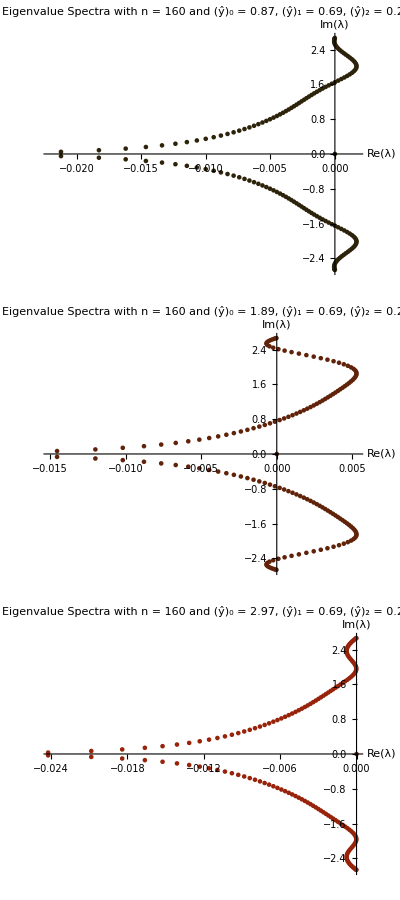
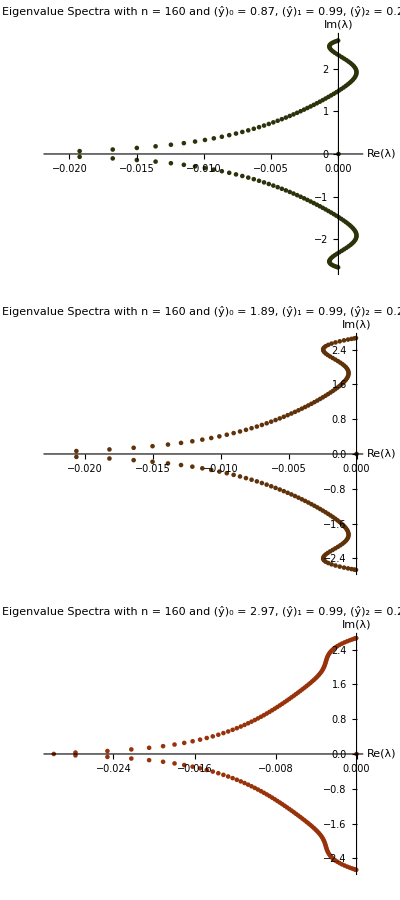
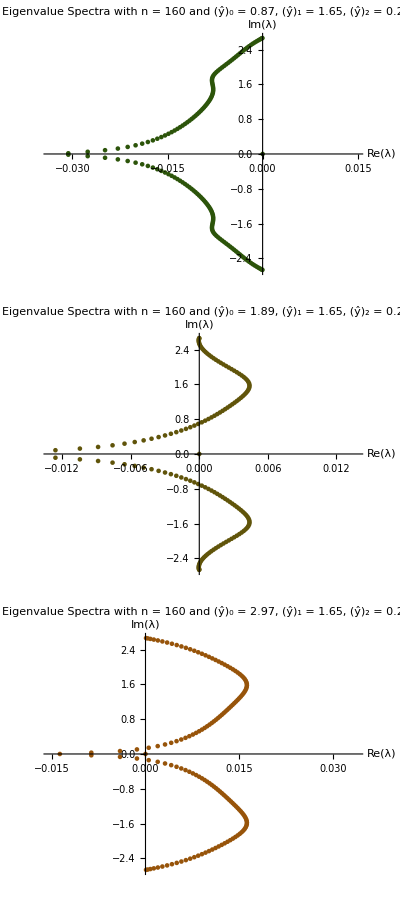
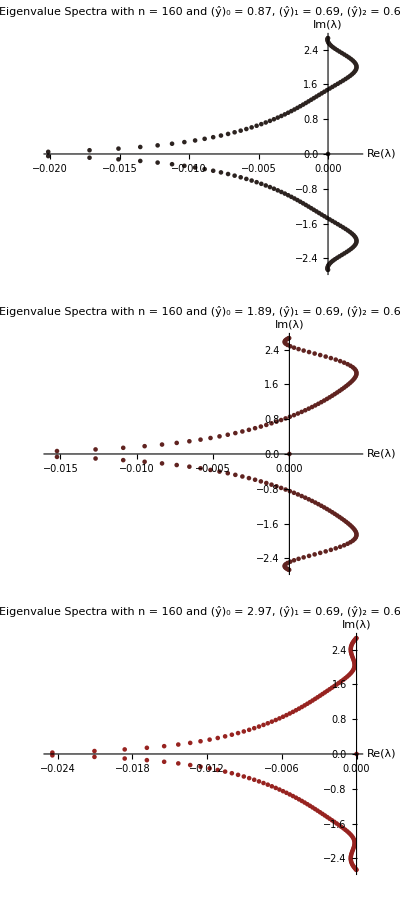
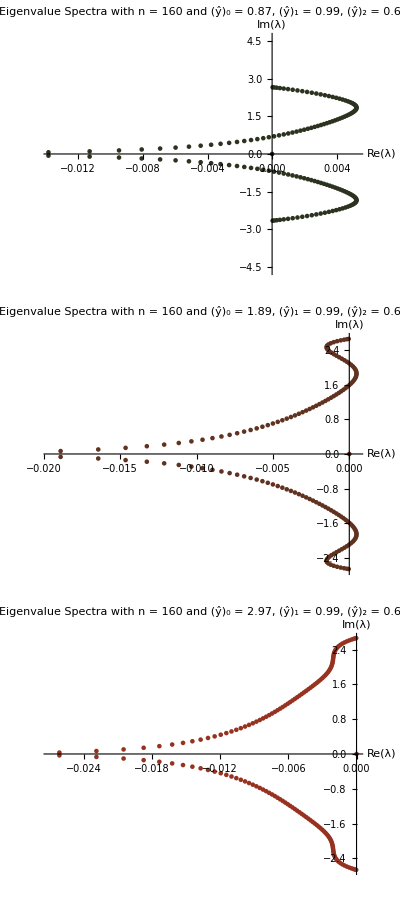
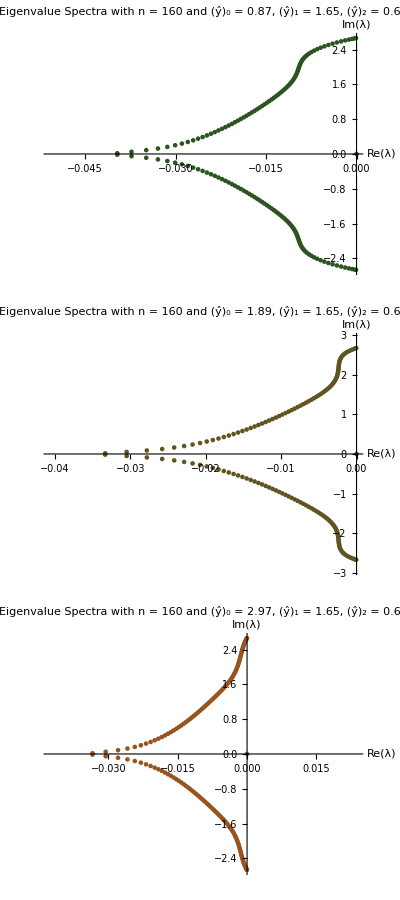
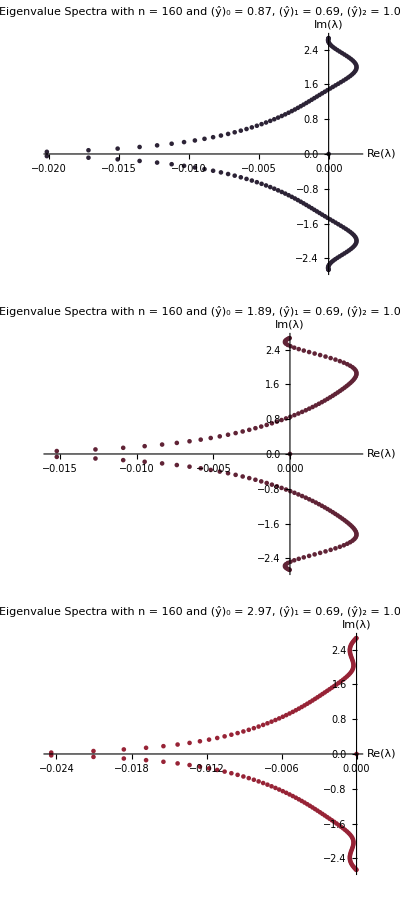
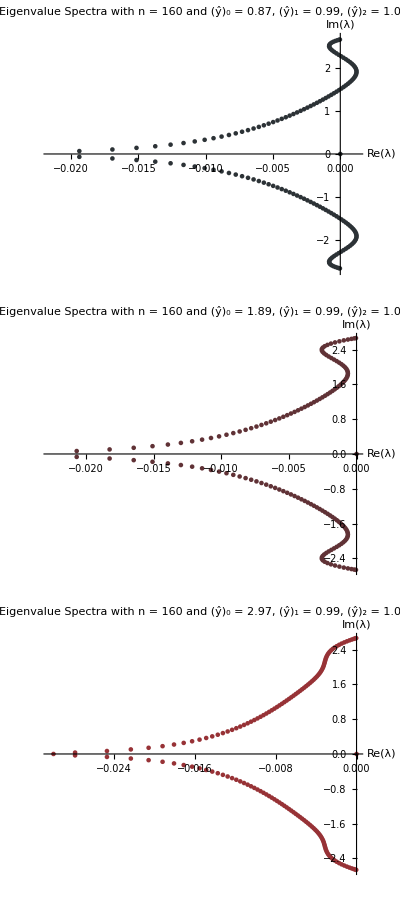
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
plotplotlist//TableForm
```

## Max(Re)

```mathematica
Clear[α,β,a1,a2,a3,yHat2,yHat1,yHat0,yHat]
Clear[γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]
Clear[γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]

yHat2List={(*1*)0.2,(*2*)0.63,(*3*)1.05,(*4*)1.14,(*5*)1.62,(*6*)2.25,(*7*)2.73,(*8*)3.39,(*9*)3.93,(*10*)4.38,(*11*)4.80};
yHat1List={(*1*)0.69,(*2*)0.99,(*3*)1.65,(*4*)1.95,(*5*)2.13,(*6*)2.55,(*7*)3.06,(*8*)3.12,(*9*)3.42,(*10*)4.23,(*11*)4.35};
yHat0List={(*1*)0.87,(*2*)1.89,(*3*)2.97,(*4*)4.17,(*5*)4.26};

maxrelist=ParallelTable[
γ22=γ22/.{bdCoeffs2[[3]]/.interiorCoeffs};
γ20=1/γ22*(γ20/.{bdCoeffs2[[1]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
γ21=1/γ22*(γ21/.{bdCoeffs2[[2]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
γ23=1/γ22*(γ23/.{bdCoeffs2[[4]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
γ24=1/γ22*(γ24/.{bdCoeffs2[[5]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a20=1/γ22*(a20/.{bdCoeffs2[[6]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a21=1/γ22*(a21/.{bdCoeffs2[[7]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a22=1/γ22*(a22/.{bdCoeffs2[[8]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a23=1/γ22*(a23/.{bdCoeffs2[[9]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a24=1/γ22*(a24/.{bdCoeffs2[[10]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a25=1/γ22*(a25/.{bdCoeffs2[[11]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a26=1/γ22*(a26/.{bdCoeffs2[[12]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
γ22=γ22/γ22/.{yHat->yHat2List[[xx]]};



γ11=γ11/.{bdCoeffs1[[2]]/.interiorCoeffs};
γ10=1/γ11*(γ10/.{bdCoeffs1[[1]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
γ12=1/γ11*(γ12/.{bdCoeffs1[[3]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
γ13=1/γ11*(γ13/.{bdCoeffs1[[4]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a10=1/γ11*(a10/.{bdCoeffs1[[5]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a11=1/γ11*(a11/.{bdCoeffs1[[6]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a12=1/γ11*(a12/.{bdCoeffs1[[7]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a13=1/γ11*(a13/.{bdCoeffs1[[8]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a14=1/γ11*(a14/.{bdCoeffs1[[9]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a15=1/γ11*(a15/.{bdCoeffs1[[10]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a16=1/γ11*(a16/.{bdCoeffs1[[11]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
γ11=γ11/γ11/.{yHat->yHat1List[[yy]]};



γ00=γ00/.{bdCoeffs0[[1]]/.interiorCoeffs};
γ01=1/γ00*(γ01/.{bdCoeffs0[[2]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
γ02=1/γ00*(γ02/.{bdCoeffs0[[3]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a00=1/γ00*(a00/.{bdCoeffs0[[4]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a01=1/γ00*(a01/.{bdCoeffs0[[5]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a02=1/γ00*(a02/.{bdCoeffs0[[6]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a03=1/γ00*(a03/.{bdCoeffs0[[7]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a04=1/γ00*(a04/.{bdCoeffs0[[8]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a05=1/γ00*(a05/.{bdCoeffs0[[9]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a06=1/γ00*(a06/.{bdCoeffs0[[10]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
γ00=γ00/γ00/.{yHat->yHat0List[[zz]]};

interior={α->0.5770460201292381,β->0.08900836845092142,a->0.6517078440898839,b->0.24815882627035918,c->0.006009630649852392};
boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};
coeff=Flatten[Join[interior,boundary]];

LHSBorders={
{1,α12,β12},
{α21,1,α22,β22},
{β31,α31,1,α32,β32}
};
RHSBorders={
{a1,b1,c1,d1,e1,f1,g1},
{a2,b2,c2,d2,e2,f2,g2},
{a3,b3,c3,d3,e3,f3,g3}
};

LHSMatrix[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{1,1}]->1,
Band[{2,1}]->α,
Band[{1,2}]->α,
Band[{3,1}]->β,
Band[{1,3}]->β
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[LHSBorders[[i]]],j++,
M[[i,j]]=LHSBorders[[i,j]]/.coeff;
M[[n-i+1,n-j+1]]=LHSBorders[[i,j]]/.coeff
]
];

M
];

RHSMatrix[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{2,1}]->-a,
Band[{3,1}]->-b,
Band[{4,1}]->-c,
Band[{1,2}]->a,
Band[{1,3}]->b,
Band[{1,4}]->c
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[RHSBorders[[i]]],j++,
M[[i,j]]=RHSBorders[[i,j]]/.coeff;
M[[n-i+1,n-j+1]]=-RHSBorders[[i,j]]/.coeff
]
];

M
];

n=160;
LHS=LHSMatrix[n,3,coeff];
RHS=RHSMatrix[n,3,coeff];

For[j=1,j<=n,j++,LHS[[1,j]]=0];
For[j=1,j<=n,j++,LHS[[j,1]]=0];
For[j=1,j<=n,j++,RHS[[1,j]]=0];
For[j=1,j<=n,j++,RHS[[j,1]]=0];
LHS[[1,1]]=1;
LHS//MatrixForm;
RHS//MatrixForm;

mat=Inverse[LHS].RHS;
eigs=-Eigenvalues[mat];
{{yHat0List[[zz]],yHat1List[[yy]],yHat2List[[xx]]},Max[Re[eigs]]},
{xx,1,Length@yHat2List},{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}];
```

```mathematica
maxrelist//TableForm;
Dimensions@maxrelist
trimmed=Flatten[maxrelist,2];

stable={};
For[i=1,i<=Length@trimmed,i++,
If[trimmed[[i,2]]<=0,
AppendTo[stable,trimmed[[i]]]]
]
stable
Length@stable
```

{11,11,5,2}

{{{2.97,0.69,0.2},0.},{{1.89,0.99,0.2},0.},{{2.97,0.99,0.2},0.},{{2.97,2.13,0.2},0.},{{0.87,2.55,0.2},0.},{{1.89,2.55,0.2},0.},{{2.97,2.55,0.2},0.},{{2.97,0.69,0.63},0.},{{2.97,0.99,0.63},0.},{{0.87,1.65,0.63},0.},{{1.89,1.65,0.63},0.},{{2.97,2.13,0.63},0.},{{2.97,2.55,0.63},0.},{{2.97,0.69,1.05},0.},{{1.89,0.99,1.05},0.},{{2.97,0.99,1.05},0.},{{0.87,3.42,1.05},0.},{{1.89,3.42,1.05},0.},{{2.97,3.42,1.05},0.},{{4.17,3.42,1.05},0.},{{2.97,0.69,1.14},0.},{{1.89,0.99,1.14},0.},{{2.97,0.99,1.14},0.},{{0.87,0.69,1.62},0.},{{0.87,0.99,1.62},0.},{{0.87,1.95,1.62},0.},{{0.87,3.42,1.62},0.},{{2.97,0.69,2.25},0.},{{1.89,0.99,2.25},0.},{{2.97,0.99,2.25},0.},{{1.89,3.42,2.25},0.},{{2.97,3.42,2.25},0.},{{2.97,4.35,2.25},0.},{{0.87,0.69,2.73},0.},{{0.87,0.99,2.73},0.},{{1.89,0.99,2.73},0.},{{2.97,0.99,2.73},0.},{{4.17,0.99,2.73},0.},{{0.87,1.65,2.73},0.},{{0.87,2.13,2.73},0.},{{1.89,2.13,2.73},0.},{{2.97,2.13,2.73},0.},{{4.17,2.13,2.73},0.},{{0.87,2.55,2.73},0.},{{1.89,2.55,2.73},0.},{{0.87,3.06,2.73},0.},{{1.89,3.12,2.73},0.},{{2.97,3.12,2.73},0.},{{4.17,3.12,2.73},0.},{{0.87,4.23,2.73},0.},{{1.89,4.23,2.73},0.},{{2.97,4.23,2.73},0.},{{4.17,4.23,2.73},0.},{{1.89,0.99,3.39},0.},{{2.97,0.99,3.39},0.},{{1.89,2.13,3.93},0.},{{2.97,2.13,3.93},0.},{{0.87,2.55,3.93},0.},{{0.87,3.42,3.93},0.},{{1.89,3.42,3.93},0.},{{0.87,4.35,3.93},0.},{{1.89,4.35,3.93},0.},{{2.97,4.35,3.93},0.},{{1.89,4.23,4.38},0.},{{2.97,4.23,4.38},0.},{{0.87,0.99,4.8},0.},{{1.89,0.99,4.8},0.},{{2.97,0.99,4.8},0.},{{4.17,0.99,4.8},0.},{{2.97,2.13,4.8},0.},{{0.87,2.55,4.8},0.},{{1.89,2.55,4.8},0.},{{2.97,2.55,4.8},0.},{{0.87,3.42,4.8},0.},{{1.89,3.42,4.8},0.},{{2.97,3.42,4.8},0.},{{0.87,4.35,4.8},0.},{{1.89,4.35,4.8},0.}}

78

```mathematica
Clear[α,β,a1,a2,a3,yHat2,yHat1,yHat0,yHat]
Clear[γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]
Clear[γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]

rk4StabilityRegion=RegionPlot[(Abs[1+(x+I y)+(x+I y)^2/2+(x+I y)^3/6+(x+I y)^4/24])<1,{x,-3,0.25},{y,-3,3},PlotStyle->Directive[Opacity[0.15]]];
stableplotlist={};
stableplotlist2={};

For[m=1,m<=Length@stable,m++,
γ22=γ22/.{bdCoeffs2[[3]]/.interiorCoeffs};
γ20=1/γ22*(γ20/.{bdCoeffs2[[1]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,3]]}])})/.{yHat->stable[[m,1,3]]};
γ21=1/γ22*(γ21/.{bdCoeffs2[[2]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,3]]}])})/.{yHat->stable[[m,1,3]]};
γ23=1/γ22*(γ23/.{bdCoeffs2[[4]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,3]]}])})/.{yHat->stable[[m,1,3]]};
γ24=1/γ22*(γ24/.{bdCoeffs2[[5]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,3]]}])})/.{yHat->stable[[m,1,3]]};
a20=1/γ22*(a20/.{bdCoeffs2[[6]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,3]]}])})/.{yHat->stable[[m,1,3]]};
a21=1/γ22*(a21/.{bdCoeffs2[[7]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,3]]}])})/.{yHat->stable[[m,1,3]]};
a22=1/γ22*(a22/.{bdCoeffs2[[8]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,3]]}])})/.{yHat->stable[[m,1,3]]};
a23=1/γ22*(a23/.{bdCoeffs2[[9]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,3]]}])})/.{yHat->stable[[m,1,3]]};
a24=1/γ22*(a24/.{bdCoeffs2[[10]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,3]]}])})/.{yHat->stable[[m,1,3]]};
a25=1/γ22*(a25/.{bdCoeffs2[[11]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,3]]}])})/.{yHat->stable[[m,1,3]]};
a26=1/γ22*(a26/.{bdCoeffs2[[12]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,3]]}])})/.{yHat->stable[[m,1,3]]};
γ22=γ22/γ22/.{yHat->stable[[m,1,3]]};



γ11=γ11/.{bdCoeffs1[[2]]/.interiorCoeffs};
γ10=1/γ11*(γ10/.{bdCoeffs1[[1]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,2]]}])})/.{yHat->stable[[m,1,2]]};
γ12=1/γ11*(γ12/.{bdCoeffs1[[3]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,2]]}])})/.{yHat->stable[[m,1,2]]};
γ13=1/γ11*(γ13/.{bdCoeffs1[[4]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,2]]}])})/.{yHat->stable[[m,1,2]]};
a10=1/γ11*(a10/.{bdCoeffs1[[5]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,2]]}])})/.{yHat->stable[[m,1,2]]};
a11=1/γ11*(a11/.{bdCoeffs1[[6]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,2]]}])})/.{yHat->stable[[m,1,2]]};
a12=1/γ11*(a12/.{bdCoeffs1[[7]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,2]]}])})/.{yHat->stable[[m,1,2]]};
a13=1/γ11*(a13/.{bdCoeffs1[[8]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,2]]}])})/.{yHat->stable[[m,1,2]]};
a14=1/γ11*(a14/.{bdCoeffs1[[9]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,2]]}])})/.{yHat->stable[[m,1,2]]};
a15=1/γ11*(a15/.{bdCoeffs1[[10]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,2]]}])})/.{yHat->stable[[m,1,2]]};
a16=1/γ11*(a16/.{bdCoeffs1[[11]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,2]]}])})/.{yHat->stable[[m,1,2]]};
γ11=γ11/γ11/.{yHat->stable[[m,1,2]]};



γ00=γ00/.{bdCoeffs0[[1]]/.interiorCoeffs};
γ01=1/γ00*(γ01/.{bdCoeffs0[[2]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,1]]}])})/.{yHat->stable[[m,1,1]]};
γ02=1/γ00*(γ02/.{bdCoeffs0[[3]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,1]]}])})/.{yHat->stable[[m,1,1]]};
a00=1/γ00*(a00/.{bdCoeffs0[[4]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,1]]}])})/.{yHat->stable[[m,1,1]]};
a01=1/γ00*(a01/.{bdCoeffs0[[5]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,1]]}])})/.{yHat->stable[[m,1,1]]};
a02=1/γ00*(a02/.{bdCoeffs0[[6]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,1]]}])})/.{yHat->stable[[m,1,1]]};
a03=1/γ00*(a03/.{bdCoeffs0[[7]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,1]]}])})/.{yHat->stable[[m,1,1]]};
a04=1/γ00*(a04/.{bdCoeffs0[[8]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,1]]}])})/.{yHat->stable[[m,1,1]]};
a05=1/γ00*(a05/.{bdCoeffs0[[9]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,1]]}])})/.{yHat->stable[[m,1,1]]};
a06=1/γ00*(a06/.{bdCoeffs0[[10]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,1]]}])})/.{yHat->stable[[m,1,1]]};
γ00=γ00/γ00/.{yHat->stable[[m,1,1]]};

interior={α->0.5770460201292381,β->0.08900836845092142,a->0.6517078440898839,b->0.24815882627035918,c->0.006009630649852392};
boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};
coeff=Flatten[Join[interior,boundary]];

LHSBorders={
{1,α12,β12},
{α21,1,α22,β22},
{β31,α31,1,α32,β32}
};
RHSBorders={
{a1,b1,c1,d1,e1,f1,g1},
{a2,b2,c2,d2,e2,f2,g2},
{a3,b3,c3,d3,e3,f3,g3}
};

LHSMatrix[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{1,1}]->1,
Band[{2,1}]->α,
Band[{1,2}]->α,
Band[{3,1}]->β,
Band[{1,3}]->β
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[LHSBorders[[i]]],j++,
M[[i,j]]=LHSBorders[[i,j]]/.coeff;
M[[n-i+1,n-j+1]]=LHSBorders[[i,j]]/.coeff
]
];

M
];

RHSMatrix[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{2,1}]->-a,
Band[{3,1}]->-b,
Band[{4,1}]->-c,
Band[{1,2}]->a,
Band[{1,3}]->b,
Band[{1,4}]->c
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[RHSBorders[[i]]],j++,
M[[i,j]]=RHSBorders[[i,j]]/.coeff;
M[[n-i+1,n-j+1]]=-RHSBorders[[i,j]]/.coeff
]
];

M
];

n=160;
LHS=LHSMatrix[n,3,coeff];
RHS=RHSMatrix[n,3,coeff];

For[j=1,j<=n,j++,LHS[[1,j]]=0];
For[j=1,j<=n,j++,LHS[[j,1]]=0];
For[j=1,j<=n,j++,RHS[[1,j]]=0];
For[j=1,j<=n,j++,RHS[[j,1]]=0];
LHS[[1,1]]=1;
LHS//MatrixForm;
RHS//MatrixForm;

mat=Inverse[LHS].RHS;
eigs=-Eigenvalues[mat];
AppendTo[stableplotlist,
ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[160]," and\n","(ŷ)_0 = ",ToString[stable[[m,1,1]]],", (ŷ)_1 = ",ToString[stable[[m,1,2]]],", (ŷ)_2 = ",ToString[stable[[m,1,3]]]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[stable[[m,1,1]]/5,stable[[m,1,2]]/5,stable[[m,1,3]]/5]]];
AppendTo[stableplotlist2,
Show[rk4StabilityRegion,ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[160]," and\n","(ŷ)_0 = ",ToString[stable[[m,1,1]]],", (ŷ)_1 = ",ToString[stable[[m,1,2]]],", (ŷ)_2 = ",ToString[stable[[m,1,3]]]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->{RGBColor[0,0,0],PointSize[0.02]}]]]
];
```

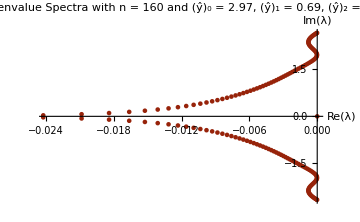
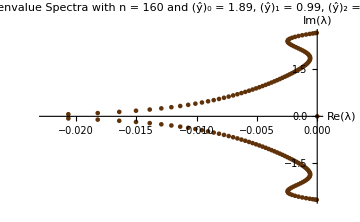
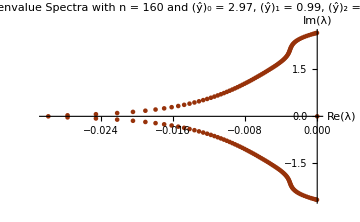
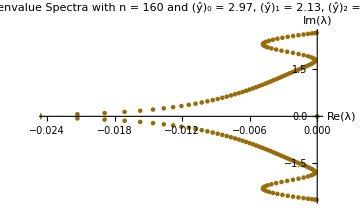
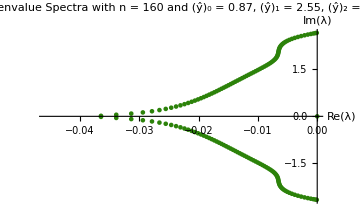
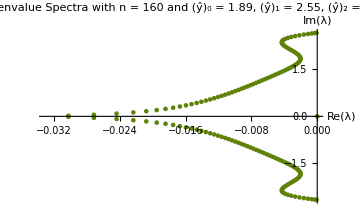
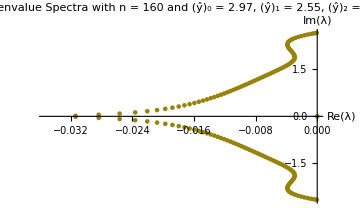
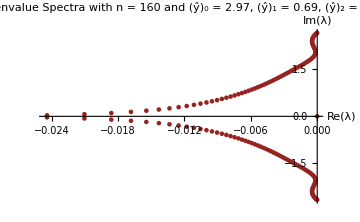

```mathematica
stableplotlist
```

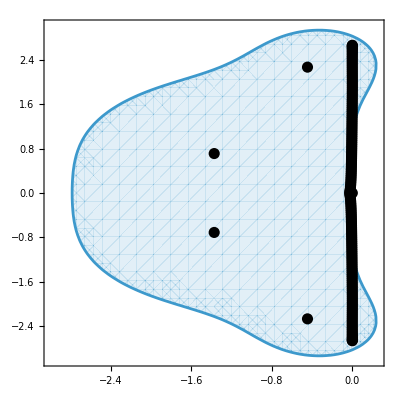
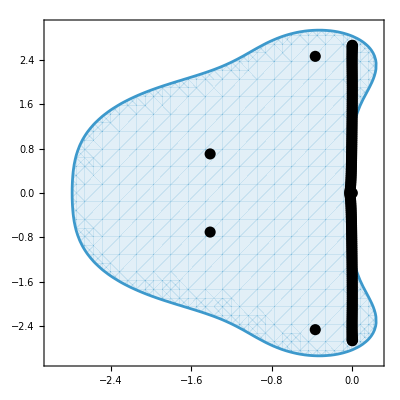
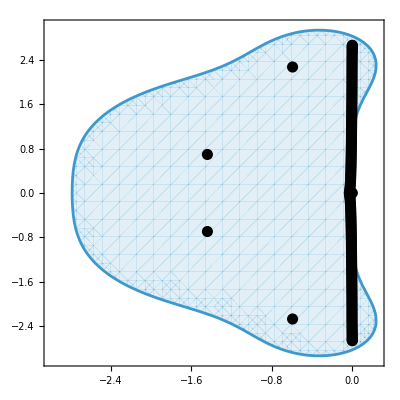
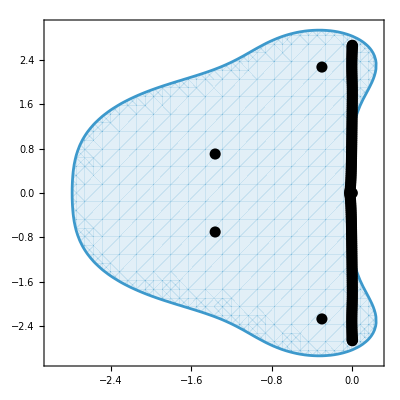
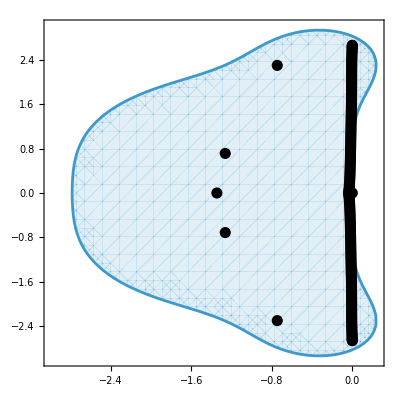
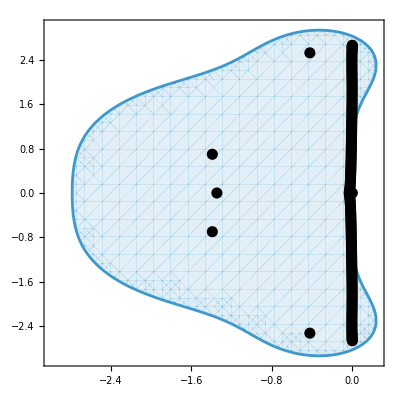
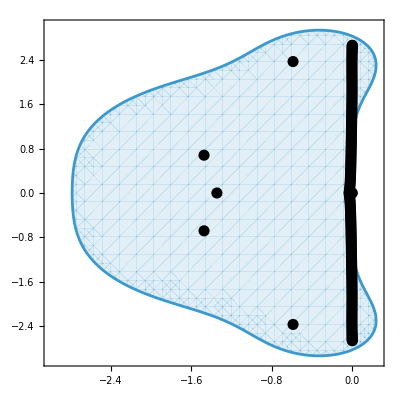
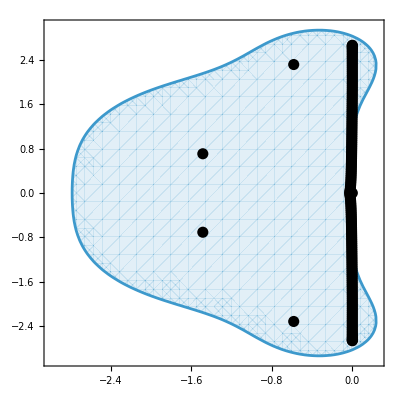
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
stableplotlist2
```

## Max(Re) Fixed

```mathematica
Clear[α,β,a1,a2,a3,yHat2,yHat1,yHat0,yHat]
Clear[γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]
Clear[γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]

LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,
If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k&&j==k-5),-a05,
If[(i==k&&j==k-6),-a06,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,
If[(i==k-1&&j==k-5),-a15,
If[(i==k-1&&j==k-6),-a16,
If[(i==k-2&&j==k),-a20,
If[(i==k-2&&j==k-1),-a21,
If[(i==k-2&&j==k-2),-a22,
If[(i==k-2&&j==k-3),-a23,
If[(i==k-2&&j==k-4),-a24,
If[(i==k-2&&j==k-5),-a25,
If[(i==k-2&&j==k-6),-a26,


If[i-3==j,-a3,
If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}];
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}];



yHat2List={(*1*)0.2,(*2*)0.63,(*3*)1.05,(*4*)1.14,(*5*)1.62,(*6*)2.25,(*7*)2.73,(*8*)3.39,(*9*)3.93,(*10*)4.38,(*11*)4.80};
yHat1List={(*1*)0.69,(*2*)0.99,(*3*)1.65,(*4*)1.95,(*5*)2.13,(*6*)2.55,(*7*)3.06,(*8*)3.12,(*9*)3.42,(*10*)4.23,(*11*)4.35};
yHat0List={(*1*)0.87,(*2*)1.89,(*3*)2.97,(*4*)4.17,(*5*)4.26};

k=160;
Clear[xx,yy,zz]
```

### Parallelization

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\natha\Documents\School\Research\Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks

```mathematica
$ProcessorCount
(*I believe these dump files allow this to now be standalone as long as you setdirectory and don't delete the files*)
(*
DumpSave["bdCoeffs0.mx","Global`bdCoeffs0"]
DumpSave["bdCoeffs1.mx","Global`bdCoeffs1"]
DumpSave["bdCoeffs2.mx","Global`bdCoeffs2"]
DumpSave["interiorCoeffs.mx","Global`interiorCoeffs"]
*)
```

10

```mathematica
LaunchKernels[8]
```

{Local (8),Local (8),Local (8),Local (8),Local (8),Local (8),Local (8),Local (8)}

```mathematica
ParallelEvaluate[Directory[]]
```

{C:\Users\natha\Documents\School\Research\Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks,C:\Users\natha\Documents\School\Research\Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks,C:\Users\natha\Documents\School\Research\Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks,C:\Users\natha\Documents\School\Research\Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks,C:\Users\natha\Documents\School\Research\Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks,C:\Users\natha\Documents\School\Research\Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks,C:\Users\natha\Documents\School\Research\Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks,C:\Users\natha\Documents\School\Research\Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks}

```mathematica
ParallelEvaluate[Get["bdCoeffs0.mx"]]
ParallelEvaluate[Get["bdCoeffs1.mx"]]
ParallelEvaluate[Get["bdCoeffs2.mx"]]
ParallelEvaluate[Get["interiorCoeffs.mx"]]
```

{Null,Null,Null,Null,Null,Null,Null,Null}

{Null,Null,Null,Null,Null,Null,Null,Null}

{Null,Null,Null,Null,Null,Null,Null,Null}

«1 more identical outputs»

```mathematica
ParallelEvaluate[ValueQ[bdCoeffs0]]
```

{True,True,True,True,True,True,True,True}

```mathematica
ParallelEvaluate[ByteCount[bdCoeffs0]/2.^30]
```

{1.96897,1.96897,1.96897,1.96897,1.96897,1.96897,1.96897,1.96897}

```mathematica
DistributeDefinitions[(*interiorCoeffs,bdCoeffs1,bdCoeffs2,*)yHat0List,yHat1List,yHat2List,LHS,RHS,LHSRows,RHSRows,k]
```

{yHat0List,yHat1List,yHat2List,LHS,LHSRows,RHS,RHSRows,k}

### Big block of code

```mathematica
(*DumpSave["maxrelist.mx","Global`maxrelist"]*)
```

{Global`maxrelist}

```mathematica
maxrelist=ParallelTable[
Print["Kernel ",$KernelID," working on ",{xx,yy,zz}];

γ22val=γ22/.{bdCoeffs2[[3]]/.interiorCoeffs};
γ20val=1/γ22val*(γ20/.{bdCoeffs2[[1]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
γ21val=1/γ22val*(γ21/.{bdCoeffs2[[2]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
γ23val=1/γ22val*(γ23/.{bdCoeffs2[[4]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
γ24val=1/γ22val*(γ24/.{bdCoeffs2[[5]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a20val=1/γ22val*(a20/.{bdCoeffs2[[6]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a21val=1/γ22val*(a21/.{bdCoeffs2[[7]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a22val=1/γ22val*(a22/.{bdCoeffs2[[8]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a23val=1/γ22val*(a23/.{bdCoeffs2[[9]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a24val=1/γ22val*(a24/.{bdCoeffs2[[10]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a25val=1/γ22val*(a25/.{bdCoeffs2[[11]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
a26val=1/γ22val*(a26/.{bdCoeffs2[[12]]/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])})/.{yHat->yHat2List[[xx]]};
γ22val=γ22val/γ22val/.{yHat->yHat2List[[xx]]};



γ11val=γ11/.{bdCoeffs1[[2]]/.interiorCoeffs};
γ10val=1/γ11val*(γ10/.{bdCoeffs1[[1]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
γ12val=1/γ11val*(γ12/.{bdCoeffs1[[3]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
γ13val=1/γ11val*(γ13/.{bdCoeffs1[[4]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a10val=1/γ11val*(a10/.{bdCoeffs1[[5]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a11val=1/γ11val*(a11/.{bdCoeffs1[[6]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a12val=1/γ11val*(a12/.{bdCoeffs1[[7]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a13val=1/γ11val*(a13/.{bdCoeffs1[[8]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a14val=1/γ11val*(a14/.{bdCoeffs1[[9]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a15val=1/γ11val*(a15/.{bdCoeffs1[[10]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
a16val=1/γ11val*(a16/.{bdCoeffs1[[11]]/.(Join[interiorCoeffs,{yHat->yHat1List[[yy]]}])})/.{yHat->yHat1List[[yy]]};
γ11val=γ11val/γ11val/.{yHat->yHat1List[[yy]]};



γ00val=γ00/.{bdCoeffs0[[1]]/.interiorCoeffs};
γ01val=1/γ00val*(γ01/.{bdCoeffs0[[2]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
γ02val=1/γ00val*(γ02/.{bdCoeffs0[[3]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a00val=1/γ00val*(a00/.{bdCoeffs0[[4]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a01val=1/γ00val*(a01/.{bdCoeffs0[[5]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a02val=1/γ00val*(a02/.{bdCoeffs0[[6]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a03val=1/γ00val*(a03/.{bdCoeffs0[[7]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a04val=1/γ00val*(a04/.{bdCoeffs0[[8]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a05val=1/γ00val*(a05/.{bdCoeffs0[[9]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
a06val=1/γ00val*(a06/.{bdCoeffs0[[10]]/.(Join[interiorCoeffs,{yHat->yHat0List[[zz]]}])})/.{yHat->yHat0List[[zz]]};
γ00val=γ00val/γ00val/.{yHat->yHat0List[[zz]]};


interior={α->0.5770460201292381,β->0.08900836845092142,a1->0.6517078440898839,a2->0.24815882627035918,a3->0.006009630649852392};
boundary={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeff=Flatten[Join[interior,boundary]];



LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeff),
γ13Bar->(γ13/(1-γ10*γ01)/.coeff),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeff),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeff),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeff)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,6}]/.coeff;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,6}]/.coeff;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2];


LHSNum=(LHS[k]/.coeff)/.barCoeffs;
RHSNum=(RHS[k]/.coeff)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];
{{yHat0List[[zz]],yHat1List[[yy]],yHat2List[[xx]]},Max[Re[eigs]]},
{xx,1,Length@yHat2List},{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}];
```

Kernel 2 working on {1,1,2}

Kernel 3 working on {1,1,3}

Kernel 4 working on {1,1,4}

Kernel 6 working on {1,2,1}

Kernel 1 working on {1,1,1}

Kernel 5 working on {1,1,5}

Kernel 7 working on {1,2,2}

Kernel 8 working on {1,2,3}

Kernel 7 working on {1,2,4}

Kernel 2 working on {1,2,5}

Kernel 3 working on {1,3,1}

Kernel 6 working on {1,3,2}

Kernel 4 working on {1,3,3}

Kernel 1 working on {1,3,4}

Kernel 5 working on {1,3,5}

Kernel 8 working on {1,4,1}

Kernel 7 working on {1,4,2}

Kernel 3 working on {1,4,3}

Kernel 2 working on {1,4,4}

Kernel 6 working on {1,4,5}

Kernel 5 working on {1,5,1}

Kernel 4 working on {1,5,2}

Kernel 1 working on {1,5,3}

Kernel 8 working on {1,5,4}

Kernel 3 working on {1,5,5}

Kernel 6 working on {1,6,1}

Kernel 7 working on {1,6,2}

Kernel 5 working on {1,6,3}

Kernel 2 working on {1,6,4}

Kernel 4 working on {1,6,5}

Kernel 1 working on {1,7,1}

Kernel 8 working on {1,7,2}

Kernel 3 working on {1,7,3}

Kernel 6 working on {1,7,4}

Kernel 7 working on {1,7,5}

Kernel 2 working on {1,8,1}

Kernel 5 working on {1,8,2}

Kernel 1 working on {1,8,3}

Kernel 4 working on {1,8,4}

Kernel 8 working on {1,8,5}

Kernel 3 working on {1,9,1}

Kernel 6 working on {1,9,2}

Kernel 7 working on {1,9,3}

Kernel 2 working on {1,9,4}

Kernel 1 working on {1,9,5}

Kernel 5 working on {1,10,1}

Kernel 4 working on {1,10,2}

Kernel 8 working on {1,10,3}

Kernel 3 working on {1,10,4}

Kernel 6 working on {1,10,5}

Kernel 7 working on {1,11,1}

Kernel 2 working on {1,11,2}

Kernel 1 working on {1,11,3}

Kernel 5 working on {1,11,4}

Kernel 4 working on {1,11,5}

Kernel 8 working on {2,1,1}

Kernel 3 working on {2,1,2}

Kernel 6 working on {2,1,3}

Kernel 2 working on {2,1,4}

Kernel 7 working on {2,1,5}

Kernel 1 working on {2,2,1}

Kernel 5 working on {2,2,2}

Kernel 4 working on {2,2,3}

Kernel 8 working on {2,2,4}

Kernel 3 working on {2,2,5}

Kernel 6 working on {2,3,1}

Kernel 2 working on {2,3,2}

Kernel 7 working on {2,3,3}

Kernel 5 working on {2,3,4}

Kernel 1 working on {2,3,5}

Kernel 4 working on {2,4,1}

Kernel 8 working on {2,4,2}

Kernel 3 working on {2,4,3}

Kernel 6 working on {2,4,4}

Kernel 2 working on {2,4,5}

Kernel 7 working on {2,5,1}

Kernel 5 working on {2,5,2}

Kernel 1 working on {2,5,3}

Kernel 4 working on {2,5,4}

Kernel 8 working on {2,5,5}

Kernel 3 working on {2,6,1}

Kernel 6 working on {2,6,2}

Kernel 2 working on {2,6,3}

Kernel 5 working on {2,6,4}

Kernel 7 working on {2,6,5}

Kernel 1 working on {2,7,1}

Kernel 4 working on {2,7,2}

Kernel 8 working on {2,7,3}

Kernel 3 working on {2,7,4}

Kernel 6 working on {2,7,5}

Kernel 2 working on {2,8,1}

Kernel 5 working on {2,8,2}

Kernel 7 working on {2,8,3}

Kernel 1 working on {2,8,4}

Kernel 4 working on {2,8,5}

Kernel 8 working on {2,9,1}

Kernel 3 working on {2,9,2}

Kernel 6 working on {2,9,3}

Kernel 2 working on {2,9,4}

Kernel 5 working on {2,9,5}

Kernel 7 working on {2,10,1}

Kernel 1 working on {2,10,2}

Kernel 4 working on {2,10,3}

Kernel 8 working on {2,10,4}

Kernel 3 working on {2,10,5}

Kernel 6 working on {2,11,1}

Kernel 2 working on {2,11,2}

Kernel 5 working on {2,11,3}

Kernel 1 working on {2,11,4}

Kernel 7 working on {2,11,5}

Kernel 4 working on {3,1,1}

Kernel 8 working on {3,1,2}

Kernel 3 working on {3,1,3}

Kernel 6 working on {3,1,4}

Kernel 2 working on {3,1,5}

Kernel 5 working on {3,2,1}

Kernel 1 working on {3,2,2}

Kernel 7 working on {3,2,3}

Kernel 4 working on {3,2,4}

Kernel 8 working on {3,2,5}

Kernel 3 working on {3,3,1}

Kernel 6 working on {3,3,2}

Kernel 2 working on {3,3,3}

Kernel 5 working on {3,3,4}

Kernel 1 working on {3,3,5}

Kernel 7 working on {3,4,1}

Kernel 4 working on {3,4,2}

Kernel 8 working on {3,4,3}

Kernel 3 working on {3,4,4}

Kernel 6 working on {3,4,5}

Kernel 2 working on {3,5,1}

Kernel 5 working on {3,5,2}

Kernel 7 working on {3,5,3}

Kernel 1 working on {3,5,4}

Kernel 4 working on {3,5,5}

Kernel 8 working on {3,6,1}

Kernel 3 working on {3,6,2}

Kernel 6 working on {3,6,3}

Kernel 2 working on {3,6,4}

Kernel 5 working on {3,6,5}

Kernel 7 working on {3,7,1}

Kernel 1 working on {3,7,2}

Kernel 4 working on {3,7,3}

Kernel 8 working on {3,7,4}

Kernel 3 working on {3,7,5}

Kernel 6 working on {3,8,1}

Kernel 2 working on {3,8,2}

Kernel 5 working on {3,8,3}

Kernel 7 working on {3,8,4}

Kernel 1 working on {3,8,5}

Kernel 4 working on {3,9,1}

Kernel 8 working on {3,9,2}

Kernel 3 working on {3,9,3}

Kernel 6 working on {3,9,4}

Kernel 2 working on {3,9,5}

Kernel 5 working on {3,10,1}

Kernel 7 working on {3,10,2}

Kernel 1 working on {3,10,3}

Kernel 4 working on {3,10,4}

Kernel 8 working on {3,10,5}

Kernel 3 working on {3,11,1}

Kernel 2 working on {3,11,2}

Kernel 6 working on {3,11,3}

Kernel 7 working on {3,11,4}

Kernel 5 working on {3,11,5}

Kernel 1 working on {4,1,1}

Kernel 4 working on {4,1,2}

Kernel 8 working on {4,1,3}

Kernel 3 working on {4,1,4}

Kernel 2 working on {4,1,5}

Kernel 6 working on {4,2,1}

Kernel 5 working on {4,2,2}

Kernel 7 working on {4,2,3}

Kernel 1 working on {4,2,4}

Kernel 4 working on {4,2,5}

Kernel 8 working on {4,3,1}

Kernel 3 working on {4,3,2}

Kernel 2 working on {4,3,3}

Kernel 6 working on {4,3,4}

Kernel 5 working on {4,3,5}

Kernel 7 working on {4,4,1}

Kernel 1 working on {4,4,2}

Kernel 4 working on {4,4,3}

Kernel 8 working on {4,4,4}

Kernel 3 working on {4,4,5}

Kernel 6 working on {4,5,1}

Kernel 2 working on {4,5,2}

Kernel 7 working on {4,5,3}

Kernel 5 working on {4,5,4}

Kernel 1 working on {4,5,5}

Kernel 4 working on {4,6,1}

Kernel 8 working on {4,6,2}

Kernel 3 working on {4,6,3}

Kernel 2 working on {4,6,4}

Kernel 6 working on {4,6,5}

Kernel 7 working on {4,7,1}

Kernel 5 working on {4,7,2}

Kernel 1 working on {4,7,3}

Kernel 4 working on {4,7,4}

Kernel 8 working on {4,7,5}

Kernel 3 working on {4,8,1}

Kernel 2 working on {4,8,2}

Kernel 7 working on {4,8,3}

Kernel 6 working on {4,8,4}

Kernel 5 working on {4,8,5}

Kernel 1 working on {4,9,1}

Kernel 4 working on {4,9,2}

Kernel 8 working on {4,9,3}

Kernel 3 working on {4,9,4}

Kernel 7 working on {4,9,5}

Kernel 6 working on {4,10,1}

Kernel 5 working on {4,10,2}

Kernel 2 working on {4,10,3}

Kernel 1 working on {4,10,4}

Kernel 4 working on {4,10,5}

Kernel 8 working on {4,11,1}

Kernel 3 working on {4,11,2}

Kernel 7 working on {4,11,3}

Kernel 2 working on {4,11,4}

Kernel 5 working on {4,11,5}

Kernel 6 working on {5,1,1}

Kernel 1 working on {5,1,2}

Kernel 4 working on {5,1,3}

Kernel 8 working on {5,1,4}

Kernel 3 working on {5,1,5}

Kernel 7 working on {5,2,1}

Kernel 5 working on {5,2,2}

Kernel 2 working on {5,2,3}

Kernel 6 working on {5,2,4}

Kernel 1 working on {5,2,5}

Kernel 4 working on {5,3,1}

Kernel 8 working on {5,3,2}

Kernel 3 working on {5,3,3}

Kernel 7 working on {5,3,4}

Kernel 5 working on {5,3,5}

Kernel 2 working on {5,4,1}

Kernel 6 working on {5,4,2}

Kernel 1 working on {5,4,3}

Kernel 4 working on {5,4,4}

Kernel 8 working on {5,4,5}

Kernel 3 working on {5,5,1}

Kernel 7 working on {5,5,2}

Kernel 5 working on {5,5,3}

Kernel 2 working on {5,5,4}

Kernel 6 working on {5,5,5}

Kernel 1 working on {5,6,1}

Kernel 4 working on {5,6,2}

Kernel 8 working on {5,6,3}

Kernel 3 working on {5,6,4}

Kernel 7 working on {5,6,5}

Kernel 5 working on {5,7,1}

Kernel 2 working on {5,7,2}

Kernel 6 working on {5,7,3}

Kernel 1 working on {5,7,4}

Kernel 4 working on {5,7,5}

Kernel 8 working on {5,8,1}

Kernel 3 working on {5,8,2}

Kernel 7 working on {5,8,3}

Kernel 2 working on {5,8,4}

Kernel 5 working on {5,8,5}

Kernel 6 working on {5,9,1}

Kernel 1 working on {5,9,2}

Kernel 4 working on {5,9,3}

Kernel 8 working on {5,9,4}

Kernel 3 working on {5,9,5}

Kernel 7 working on {5,10,1}

Kernel 2 working on {5,10,2}

Kernel 5 working on {5,10,3}

Kernel 6 working on {5,10,4}

Kernel 1 working on {5,10,5}

Kernel 4 working on {5,11,1}

Kernel 8 working on {5,11,2}

Kernel 3 working on {5,11,3}

Kernel 7 working on {5,11,4}

Kernel 2 working on {5,11,5}

Kernel 6 working on {6,1,1}

Kernel 5 working on {6,1,2}

Kernel 1 working on {6,1,3}

Kernel 4 working on {6,1,4}

Kernel 8 working on {6,1,5}

Kernel 3 working on {6,2,1}

Kernel 7 working on {6,2,2}

Kernel 2 working on {6,2,3}

Kernel 6 working on {6,2,4}

Kernel 5 working on {6,2,5}

Kernel 1 working on {6,3,1}

Kernel 4 working on {6,3,2}

Kernel 8 working on {6,3,3}

Kernel 3 working on {6,3,4}

Kernel 7 working on {6,3,5}

Kernel 2 working on {6,4,1}

Kernel 6 working on {6,4,2}

Kernel 5 working on {6,4,3}

Kernel 1 working on {6,4,4}

Kernel 4 working on {6,4,5}

Kernel 8 working on {6,5,1}

Kernel 3 working on {6,5,2}

Kernel 7 working on {6,5,3}

Kernel 2 working on {6,5,4}

Kernel 6 working on {6,5,5}

Kernel 5 working on {6,6,1}

Kernel 1 working on {6,6,2}

Kernel 4 working on {6,6,3}

Kernel 8 working on {6,6,4}

Kernel 3 working on {6,6,5}

Kernel 7 working on {6,7,1}

Kernel 2 working on {6,7,2}

Kernel 6 working on {6,7,3}

Kernel 5 working on {6,7,4}

Kernel 1 working on {6,7,5}

Kernel 4 working on {6,8,1}

Kernel 8 working on {6,8,2}

Kernel 3 working on {6,8,3}

Kernel 2 working on {6,8,4}

Kernel 7 working on {6,8,5}

Kernel 6 working on {6,9,1}

Kernel 5 working on {6,9,2}

Kernel 1 working on {6,9,3}

Kernel 4 working on {6,9,4}

Kernel 8 working on {6,9,5}

Kernel 3 working on {6,10,1}

Kernel 2 working on {6,10,2}

Kernel 6 working on {6,10,3}

Kernel 7 working on {6,10,4}

Kernel 5 working on {6,10,5}

Kernel 1 working on {6,11,1}

Kernel 4 working on {6,11,2}

Kernel 8 working on {6,11,3}

Kernel 3 working on {6,11,4}

Kernel 2 working on {6,11,5}

Kernel 6 working on {7,1,1}

Kernel 7 working on {7,1,2}

Kernel 5 working on {7,1,3}

Kernel 1 working on {7,1,4}

Kernel 4 working on {7,1,5}

Kernel 8 working on {7,2,1}

Kernel 3 working on {7,2,2}

Kernel 7 working on {7,2,3}

Kernel 2 working on {7,2,4}

Kernel 6 working on {7,2,5}

Kernel 5 working on {7,3,1}

Kernel 1 working on {7,3,2}

Kernel 4 working on {7,3,3}

Kernel 8 working on {7,3,4}

Kernel 3 working on {7,3,5}

Kernel 7 working on {7,4,1}

Kernel 2 working on {7,4,2}

Kernel 6 working on {7,4,3}

Kernel 5 working on {7,4,4}

Kernel 1 working on {7,4,5}

Kernel 4 working on {7,5,1}

Kernel 8 working on {7,5,2}

Kernel 3 working on {7,5,3}

Kernel 7 working on {7,5,4}

Kernel 2 working on {7,5,5}

Kernel 6 working on {7,6,1}

Kernel 5 working on {7,6,2}

Kernel 1 working on {7,6,3}

Kernel 4 working on {7,6,4}

Kernel 8 working on {7,6,5}

Kernel 3 working on {7,7,1}

Kernel 7 working on {7,7,2}

Kernel 2 working on {7,7,3}

Kernel 6 working on {7,7,4}

Kernel 5 working on {7,7,5}

Kernel 1 working on {7,8,1}

Kernel 4 working on {7,8,2}

Kernel 3 working on {7,8,3}

Kernel 8 working on {7,8,4}

Kernel 7 working on {7,8,5}

Kernel 2 working on {7,9,1}

Kernel 6 working on {7,9,2}

Kernel 5 working on {7,9,3}

Kernel 1 working on {7,9,4}

Kernel 4 working on {7,9,5}

Kernel 3 working on {7,10,1}

Kernel 8 working on {7,10,2}

Kernel 7 working on {7,10,3}

Kernel 2 working on {7,10,4}

Kernel 6 working on {7,10,5}

Kernel 5 working on {7,11,1}

Kernel 1 working on {7,11,2}

Kernel 4 working on {7,11,3}

Kernel 3 working on {7,11,4}

Kernel 7 working on {7,11,5}

Kernel 2 working on {8,1,1}

Kernel 8 working on {8,1,2}

Kernel 6 working on {8,1,3}

Kernel 5 working on {8,1,4}

Kernel 1 working on {8,1,5}

Kernel 4 working on {8,2,1}

Kernel 3 working on {8,2,2}

Kernel 7 working on {8,2,3}

Kernel 2 working on {8,2,4}

Kernel 6 working on {8,2,5}

Kernel 8 working on {8,3,1}

Kernel 5 working on {8,3,2}

Kernel 1 working on {8,3,3}

Kernel 4 working on {8,3,4}

Kernel 3 working on {8,3,5}

Kernel 7 working on {8,4,1}

Kernel 2 working on {8,4,2}

Kernel 6 working on {8,4,3}

Kernel 5 working on {8,4,4}

Kernel 8 working on {8,4,5}

Kernel 1 working on {8,5,1}

Kernel 4 working on {8,5,2}

Kernel 3 working on {8,5,3}

Kernel 7 working on {8,5,4}

Kernel 2 working on {8,5,5}

Kernel 6 working on {8,6,1}

Kernel 5 working on {8,6,2}

Kernel 8 working on {8,6,3}

Kernel 1 working on {8,6,4}

Kernel 4 working on {8,6,5}

Kernel 3 working on {8,7,1}

Kernel 7 working on {8,7,2}

Kernel 2 working on {8,7,3}

Kernel 6 working on {8,7,4}

Kernel 5 working on {8,7,5}

Kernel 8 working on {8,8,1}

Kernel 1 working on {8,8,2}

Kernel 4 working on {8,8,3}

Kernel 3 working on {8,8,4}

Kernel 2 working on {8,8,5}

Kernel 7 working on {8,9,1}

Kernel 6 working on {8,9,2}

Kernel 5 working on {8,9,3}

Kernel 8 working on {8,9,4}

Kernel 1 working on {8,9,5}

Kernel 4 working on {8,10,1}

Kernel 3 working on {8,10,2}

Kernel 2 working on {8,10,3}

Kernel 7 working on {8,10,4}

Kernel 6 working on {8,10,5}

Kernel 5 working on {8,11,1}

Kernel 8 working on {8,11,2}

Kernel 1 working on {8,11,3}

Kernel 4 working on {8,11,4}

Kernel 3 working on {8,11,5}

Kernel 2 working on {9,1,1}

Kernel 7 working on {9,1,2}

Kernel 6 working on {9,1,3}

Kernel 5 working on {9,1,4}

Kernel 8 working on {9,1,5}

Kernel 1 working on {9,2,1}

Kernel 4 working on {9,2,2}

Kernel 3 working on {9,2,3}

Kernel 2 working on {9,2,4}

Kernel 7 working on {9,2,5}

Kernel 6 working on {9,3,1}

Kernel 5 working on {9,3,2}

Kernel 1 working on {9,3,3}

Kernel 8 working on {9,3,4}

Kernel 4 working on {9,3,5}

Kernel 3 working on {9,4,1}

Kernel 2 working on {9,4,2}

Kernel 7 working on {9,4,3}

Kernel 6 working on {9,4,4}

Kernel 5 working on {9,4,5}

Kernel 1 working on {9,5,1}

Kernel 8 working on {9,5,2}

Kernel 4 working on {9,5,3}

Kernel 3 working on {9,5,4}

Kernel 2 working on {9,5,5}

Kernel 7 working on {9,6,1}

Kernel 6 working on {9,6,2}

Kernel 5 working on {9,6,3}

Kernel 1 working on {9,6,4}

Kernel 8 working on {9,6,5}

Kernel 4 working on {9,7,1}

Kernel 3 working on {9,7,2}

Kernel 2 working on {9,7,3}

Kernel 7 working on {9,7,4}

Kernel 6 working on {9,7,5}

Kernel 5 working on {9,8,1}

Kernel 1 working on {9,8,2}

Kernel 8 working on {9,8,3}

Kernel 4 working on {9,8,4}

Kernel 3 working on {9,8,5}

Kernel 2 working on {9,9,1}

Kernel 7 working on {9,9,2}

Kernel 6 working on {9,9,3}

Kernel 5 working on {9,9,4}

Kernel 1 working on {9,9,5}

Kernel 8 working on {9,10,1}

Kernel 4 working on {9,10,2}

Kernel 3 working on {9,10,3}

Kernel 2 working on {9,10,4}

Kernel 7 working on {9,10,5}

Kernel 6 working on {9,11,1}

Kernel 5 working on {9,11,2}

Kernel 1 working on {9,11,3}

Kernel 8 working on {9,11,4}

Kernel 4 working on {9,11,5}

Kernel 3 working on {10,1,1}

Kernel 2 working on {10,1,2}

Kernel 7 working on {10,1,3}

Kernel 6 working on {10,1,4}

Kernel 5 working on {10,1,5}

Kernel 1 working on {10,2,1}

Kernel 8 working on {10,2,2}

Kernel 4 working on {10,2,3}

Kernel 3 working on {10,2,4}

Kernel 2 working on {10,2,5}

Kernel 7 working on {10,3,1}

Kernel 6 working on {10,3,2}

Kernel 5 working on {10,3,3}

Kernel 1 working on {10,3,4}

Kernel 8 working on {10,3,5}

Kernel 4 working on {10,4,1}

Kernel 3 working on {10,4,2}

Kernel 2 working on {10,4,3}

Kernel 7 working on {10,4,4}

Kernel 6 working on {10,4,5}

Kernel 5 working on {10,5,1}

Kernel 1 working on {10,5,2}

Kernel 8 working on {10,5,3}

Kernel 4 working on {10,5,4}

Kernel 3 working on {10,5,5}

Kernel 2 working on {10,6,1}

Kernel 7 working on {10,6,2}

Kernel 6 working on {10,6,3}

Kernel 5 working on {10,6,4}

Kernel 1 working on {10,6,5}

Kernel 8 working on {10,7,1}

Kernel 4 working on {10,7,2}

Kernel 3 working on {10,7,3}

Kernel 2 working on {10,7,4}

Kernel 7 working on {10,7,5}

Kernel 6 working on {10,8,1}

Kernel 5 working on {10,8,2}

Kernel 1 working on {10,8,3}

Kernel 8 working on {10,8,4}

Kernel 4 working on {10,8,5}

Kernel 3 working on {10,9,1}

Kernel 2 working on {10,9,2}

Kernel 7 working on {10,9,3}

Kernel 6 working on {10,9,4}

Kernel 5 working on {10,9,5}

Kernel 1 working on {10,10,1}

Kernel 8 working on {10,10,2}

Kernel 4 working on {10,10,3}

Kernel 3 working on {10,10,4}

Kernel 2 working on {10,10,5}

Kernel 7 working on {10,11,1}

Kernel 6 working on {10,11,2}

Kernel 5 working on {10,11,3}

Kernel 1 working on {10,11,4}

Kernel 8 working on {10,11,5}

Kernel 4 working on {11,1,1}

Kernel 3 working on {11,1,2}

Kernel 2 working on {11,1,3}

Kernel 7 working on {11,1,4}

Kernel 6 working on {11,1,5}

Kernel 5 working on {11,2,1}

Kernel 1 working on {11,2,2}

Kernel 8 working on {11,2,3}

Kernel 4 working on {11,2,4}

Kernel 3 working on {11,2,5}

Kernel 2 working on {11,3,1}

Kernel 7 working on {11,3,2}

Kernel 6 working on {11,3,3}

Kernel 5 working on {11,3,4}

Kernel 1 working on {11,3,5}

Kernel 8 working on {11,4,1}

Kernel 4 working on {11,4,2}

Kernel 3 working on {11,4,3}

Kernel 2 working on {11,4,4}

Kernel 7 working on {11,4,5}

Kernel 6 working on {11,5,1}

Kernel 5 working on {11,5,2}

Kernel 1 working on {11,5,3}

Kernel 8 working on {11,5,4}

Kernel 4 working on {11,5,5}

Kernel 3 working on {11,6,1}

Kernel 2 working on {11,6,2}

Kernel 7 working on {11,6,3}

Kernel 6 working on {11,6,4}

Kernel 5 working on {11,6,5}

Kernel 1 working on {11,7,1}

Kernel 8 working on {11,7,2}

Kernel 4 working on {11,7,3}

Kernel 3 working on {11,7,4}

Kernel 2 working on {11,7,5}

Kernel 7 working on {11,8,1}

Kernel 6 working on {11,8,2}

Kernel 5 working on {11,8,3}

Kernel 1 working on {11,8,4}

Kernel 8 working on {11,8,5}

Kernel 4 working on {11,9,1}

Kernel 3 working on {11,9,2}

Kernel 2 working on {11,9,3}

Kernel 7 working on {11,9,4}

Kernel 6 working on {11,9,5}

Kernel 5 working on {11,10,1}

Kernel 1 working on {11,10,2}

Kernel 8 working on {11,10,3}

Kernel 4 working on {11,10,4}

Kernel 3 working on {11,10,5}

Kernel 2 working on {11,11,1}

Kernel 7 working on {11,11,2}

Kernel 6 working on {11,11,3}

Kernel 5 working on {11,11,4}

Kernel 1 working on {11,11,5}

### Block 2 - Trimming to stable only

```mathematica
Get["maxrelist.mx"]
```

```mathematica
maxrelist//TableForm
Dimensions@maxrelist
trimmed=Flatten[maxrelist,2];

stable={};
For[i=1,i<=Length@trimmed,i++,
If[trimmed[[i,2]]<=0,
AppendTo[stable,trimmed[[i]]]]
]
stable
Length@stable
```

0.87
0.69
0.2 | 0.00370991
1.89
0.69
0.2 | 0.0111186
2.97
0.69
0.2 | 0.147291
4.17
0.69
0.2 | 0.493196
4.26
0.69
0.2 | 3.97985 | 0.87
0.99
0.2 | 0.00217669
1.89
0.99
0.2 | 0.00742813
2.97
0.99
0.2 | 0.206115
4.17
0.99
0.2 | 0.39163
4.26
0.99
0.2 | 0.290873 | 0.87
1.65
0.2 | 0.00686492
1.89
1.65
0.2 | 0.00409089
2.97
1.65
0.2 | 0.227377
4.17
1.65
0.2 | 0.192879
4.26
1.65
0.2 | 0.0786412 | 0.87
1.95
0.2 | 0.00944871
1.89
1.95
0.2 | 0.00658153
2.97
1.95
0.2 | 0.00560797
4.17
1.95
0.2 | 0.899095
4.26
1.95
0.2 | 0.0123911 | 0.87
2.13
0.2 | 0.016068
1.89
2.13
0.2 | 0.00445063
2.97
2.13
0.2 | 0.0446826
4.17
2.13
0.2 | 0.474341
4.26
2.13
0.2 | 43.9324 | 0.87
2.55
0.2 | 0.314104
1.89
2.55
0.2 | 0.00274006
2.97
2.55
0.2 | 0.113729
4.17
2.55
0.2 | 0.348803
4.26
2.55
0.2 | 0.338476 | 0.87
3.06
0.2 | 0.19087
1.89
3.06
0.2 | 0.00163145
2.97
3.06
0.2 | 0.159668
4.17
3.06
0.2 | 0.456035
4.26
3.06
0.2 | 0.212747 | 0.87
3.12
0.2 | 0.201018
1.89
3.12
0.2 | 1.49672
2.97
3.12
0.2 | 0.157895
4.17
3.12
0.2 | 1.73077
4.26
3.12
0.2 | 0.206948 | 0.87
3.42
0.2 | 0.737666
1.89
3.42
0.2 | 0.00522346
2.97
3.42
0.2 | 0.159796
4.17
3.42
0.2 | 0.294628
4.26
3.42
0.2 | 0.687212 | 0.87
4.23
0.2 | 1.44782
1.89
4.23
0.2 | 0.0271597
2.97
4.23
0.2 | 0.20518
4.17
4.23
0.2 | 0.242783
4.26
4.23
0.2 | 4.4524 | 0.87
4.35
0.2 | 13.7383
1.89
4.35
0.2 | 0.00722745
2.97
4.35
0.2 | 0.154801
4.17
4.35
0.2 | 0.23778
4.26
4.35
0.2 | 0.00460654
0.87
0.69
0.63 | 0.00528961
1.89
0.69
0.63 | 0.0104879
2.97
0.69
0.63 | 0.217047
4.17
0.69
0.63 | 2.05803
4.26
0.69
0.63 | 6.35375 | 0.87
0.99
0.63 | 0.00135212
1.89
0.99
0.63 | 0.00883387
2.97
0.99
0.63 | 0.328872
4.17
0.99
0.63 | 10.0068
4.26
0.99
0.63 | 4.18859 | 0.87
1.65
0.63 | 0.00968873
1.89
1.65
0.63 | 0.0075007
2.97
1.65
0.63 | 6.22897
4.17
1.65
0.63 | 8.61914
4.26
1.65
0.63 | 3.2046 | 0.87
1.95
0.63 | 0.0100095
1.89
1.95
0.63 | 0.00968782
2.97
1.95
0.63 | 0.00400525
4.17
1.95
0.63 | 0.00692482
4.26
1.95
0.63 | 0.903767 | 0.87
2.13
0.63 | 0.0101971
1.89
2.13
0.63 | 0.00751622
2.97
2.13
0.63 | 0.0338837
4.17
2.13
0.63 | 0.132366
4.26
2.13
0.63 | 22.5387 | 0.87
2.55
0.63 | 2.46989
1.89
2.55
0.63 | 0.00609304
2.97
2.55
0.63 | 0.140028
4.17
2.55
0.63 | 4.05519
4.26
2.55
0.63 | 5.07271 | 0.87
3.06
0.63 | 0.251784
1.89
3.06
0.63 | 0.0240124
2.97
3.06
0.63 | 0.204303
4.17
3.06
0.63 | 0.0792607
4.26
3.06
0.63 | 2.61584 | 0.87
3.12
0.63 | 0.220135
1.89
3.12
0.63 | 1.54158
2.97
3.12
0.63 | 0.196069
4.17
3.12
0.63 | 0.140052
4.26
3.12
0.63 | 1.64074 | 0.87
3.42
0.63 | 0.132586
1.89
3.42
0.63 | 0.0181495
2.97
3.42
0.63 | 0.192347
4.17
3.42
0.63 | 0.606778
4.26
3.42
0.63 | 9.38397 | 0.87
4.23
0.63 | 2.42877
1.89
4.23
0.63 | 0.523249
2.97
4.23
0.63 | 1.8271
4.17
4.23
0.63 | 3.01877
4.26
4.23
0.63 | 11.6685 | 0.87
4.35
0.63 | 0.124245
1.89
4.35
0.63 | 0.0143602
2.97
4.35
0.63 | 0.215769
4.17
4.35
0.63 | 3.14366
4.26
4.35
0.63 | 5.99486
0.87
0.69
1.05 | 0.0031788
1.89
0.69
1.05 | 0.0100769
2.97
0.69
1.05 | 0.211461
4.17
0.69
1.05 | 1.91003
4.26
0.69
1.05 | 6.28589 | 0.87
0.99
1.05 | 0.00176513
1.89
0.99
1.05 | 0.00704724
2.97
0.99
1.05 | 0.193548
4.17
0.99
1.05 | 0.388744
4.26
0.99
1.05 | 0.276912 | 0.87
1.65
1.05 | 0.00666026
1.89
1.65
1.05 | -7.48026×10^-6
2.97
1.65
1.05 | 0.348888
4.17
1.65
1.05 | 0.0119891
4.26
1.65
1.05 | 0.00594918 | 0.87
1.95
1.05 | 0.00943599
1.89
1.95
1.05 | 0.00553515
2.97
1.95
1.05 | 0.234359
4.17
1.95
1.05 | 2.44199
4.26
1.95
1.05 | 0.00782813 | 0.87
2.13
1.05 | 0.0152244
1.89
2.13
1.05 | 0.00139321
2.97
2.13
1.05 | 0.210964
4.17
2.13
1.05 | 11.6437
4.26
2.13
1.05 | 1.45704 | 0.87
2.55
1.05 | 0.432177
1.89
2.55
1.05 | 0.218306
2.97
2.55
1.05 | 0.0155374
4.17
2.55
1.05 | 0.413834
4.26
2.55
1.05 | 0.41209 | 0.87
3.06
1.05 | 0.202176
1.89
3.06
1.05 | 0.672443
2.97
3.06
1.05 | 0.157053
4.17
3.06
1.05 | 0.174372
4.26
3.06
1.05 | 0.178956 | 0.87
3.12
1.05 | 0.205917
1.89
3.12
1.05 | 0.56696
2.97
3.12
1.05 | 0.0971662
4.17
3.12
1.05 | 0.189502
4.26
3.12
1.05 | 0.189124 | 0.87
3.42
1.05 | 0.286899
1.89
3.42
1.05 | 0.237265
2.97
3.42
1.05 | 0.361975
4.17
3.42
1.05 | 0.275865
4.26
3.42
1.05 | 0.285738 | 0.87
4.23
1.05 | 1.63331
1.89
4.23
1.05 | 1.2992
2.97
4.23
1.05 | 0.158148
4.17
4.23
1.05 | 13.4552
4.26
4.23
1.05 | 2.68783 | 0.87
4.35
1.05 | 15.1065
1.89
4.35
1.05 | 94.1173
2.97
4.35
1.05 | 20.5793
4.17
4.35
1.05 | 20.8199
4.26
4.35
1.05 | 17.555
0.87
0.69
1.14 | 0.00292866
1.89
0.69
1.14 | 0.00978143
2.97
0.69
1.14 | 0.230767
4.17
0.69
1.14 | 2.7692
4.26
0.69
1.14 | 6.99058 | 0.87
0.99
1.14 | 0.00146102
1.89
0.99
1.14 | 0.0069323
2.97
0.99
1.14 | 0.218963
4.17
0.99
1.14 | 0.386113
4.26
0.99
1.14 | 0.311214 | 0.87
1.65
1.14 | 0.00667723
1.89
1.65
1.14 | -0.0000116672
2.97
1.65
1.14 | 0.303635
4.17
1.65
1.14 | 0.0126504
4.26
1.65
1.14 | 0.00633746 | 0.87
1.95
1.14 | 0.00948553
1.89
1.95
1.14 | 0.00563738
2.97
1.95
1.14 | 0.229244
4.17
1.95
1.14 | 2.36981
4.26
1.95
1.14 | 0.00757972 | 0.87
2.13
1.14 | 0.0139563
1.89
2.13
1.14 | 0.00208916
2.97
2.13
1.14 | 0.212225
4.17
2.13
1.14 | 8.18159
4.26
2.13
1.14 | 1.12575 | 0.87
2.55
1.14 | 0.665451
1.89
2.55
1.14 | 0.113261
2.97
2.55
1.14 | 0.107623
4.17
2.55
1.14 | 0.616172
4.26
2.55
1.14 | 0.622048 | 0.87
3.06
1.14 | 0.215665
1.89
3.06
1.14 | 0.643364
2.97
3.06
1.14 | 0.18563
4.17
3.06
1.14 | 0.181171
4.26
3.06
1.14 | 0.190854 | 0.87
3.12
1.14 | 0.210926
1.89
3.12
1.14 | 0.566704
2.97
3.12
1.14 | 0.14804
4.17
3.12
1.14 | 0.185982
4.26
3.12
1.14 | 0.1909 | 0.87
3.42
1.14 | 0.233012
1.89
3.42
1.14 | 0.250966
2.97
3.42
1.14 | 0.491353
4.17
3.42
1.14 | 0.229028
4.26
3.42
1.14 | 0.233349 | 0.87
4.23
1.14 | 1.84188
1.89
4.23
1.14 | 1.26417
2.97
4.23
1.14 | 0.19305
4.17
4.23
1.14 | 4.67643
4.26
4.23
1.14 | 2.44637 | 0.87
4.35
1.14 | 4.28146
1.89
4.35
1.14 | 28.1733
2.97
4.35
1.14 | 0.524767
4.17
4.35
1.14 | 5.67139
4.26
4.35
1.14 | 4.85808
0.87
0.69
1.62 | 0.00808822
1.89
0.69
1.62 | 0.0083357
2.97
0.69
1.62 | 10.062
4.17
0.69
1.62 | 1.49861
4.26
0.69
1.62 | 48.3294 | 0.87
0.99
1.62 | 0.100829
1.89
0.99
1.62 | 0.00893766
2.97
0.99
1.62 | 12.3495
4.17
0.99
1.62 | 0.00729805
4.26
0.99
1.62 | 0.0024336 | 0.87
1.65
1.62 | 0.00511377
1.89
1.65
1.62 | 0.00375924
2.97
1.65
1.62 | 3.93955
4.17
1.65
1.62 | 2.83299
4.26
1.65
1.62 | 0.17256 | 0.87
1.95
1.62 | 0.0132883
1.89
1.95
1.62 | 0.00542205
2.97
1.95
1.62 | 16.1768
4.17
1.95
1.62 | 0.00806503
4.26
1.95
1.62 | 0.00534997 | 0.87
2.13
1.62 | 0.00806977
1.89
2.13
1.62 | 0.0018365
2.97
2.13
1.62 | 25.4533
4.17
2.13
1.62 | 0.00748613
4.26
2.13
1.62 | 0.0051134 | 0.87
2.55
1.62 | 0.00460939
1.89
2.55
1.62 | 0.00318002
2.97
2.55
1.62 | 18.2555
4.17
2.55
1.62 | 0.00565308
4.26
2.55
1.62 | 0.00433842 | 0.87
3.06
1.62 | 1.86129
1.89
3.06
1.62 | 7.12674
2.97
3.06
1.62 | 31.6867
4.17
3.06
1.62 | 0.197992
4.26
3.06
1.62 | 0.433279 | 0.87
3.12
1.62 | 0.252028
1.89
3.12
1.62 | 0.328499
2.97
3.12
1.62 | 377.101
4.17
3.12
1.62 | 0.139393
4.26
3.12
1.62 | 0.195923 | 0.87
3.42
1.62 | 0.0573975
1.89
3.42
1.62 | 0.0389747
2.97
3.42
1.62 | 0.669246
4.17
3.42
1.62 | 0.0585765
4.26
3.42
1.62 | 0.053987 | 0.87
4.23
1.62 | 3.9632
1.89
4.23
1.62 | 8.2341
2.97
4.23
1.62 | 17.7795
4.17
4.23
1.62 | 0.0493994
4.26
4.23
1.62 | 0.966894 | 0.87
4.35
1.62 | 0.0893272
1.89
4.35
1.62 | 0.104455
2.97
4.35
1.62 | 8.45437
4.17
4.35
1.62 | 0.0506288
4.26
4.35
1.62 | 0.0611935
0.87
0.69
2.25 | 0.00538717
1.89
0.69
2.25 | 0.00809026
2.97
0.69
2.25 | 0.0797587
4.17
0.69
2.25 | 0.18962
4.26
0.69
2.25 | 4.51634 | 0.87
0.99
2.25 | 0.00383564
1.89
0.99
2.25 | 0.00683288
2.97
0.99
2.25 | 0.0537654
4.17
0.99
2.25 | 0.0181048
4.26
0.99
2.25 | 0.0189295 | 0.87
1.65
2.25 | 0.00676432
1.89
1.65
2.25 | 0.00280835
2.97
1.65
2.25 | 0.293337
4.17
1.65
2.25 | 0.00891899
4.26
1.65
2.25 | 0.00593719 | 0.87
1.95
2.25 | 0.00825216
1.89
1.95
2.25 | 0.00520442
2.97
1.95
2.25 | 0.125225
4.17
1.95
2.25 | 2.31908
4.26
1.95
2.25 | 0.00658615 | 0.87
2.13
2.25 | 0.0125555
1.89
2.13
2.25 | 0.00395593
2.97
2.13
2.25 | 0.0874449
4.17
2.13
2.25 | 13.5378
4.26
2.13
2.25 | 1.68489 | 0.87
2.55
2.25 | 0.00882078
1.89
2.55
2.25 | 0.00874212
2.97
2.55
2.25 | 1.80061
4.17
2.55
2.25 | 0.0102211
4.26
2.55
2.25 | 0.00705924 | 0.87
3.06
2.25 | 0.0976562
1.89
3.06
2.25 | 0.612043
2.97
3.06
2.25 | 0.0116588
4.17
3.06
2.25 | 0.114364
4.26
3.06
2.25 | 0.0907148 | 0.87
3.12
2.25 | 0.13918
1.89
3.12
2.25 | 0.532782
2.97
3.12
2.25 | 0.00429895
4.17
3.12
2.25 | 0.160218
4.26
3.12
2.25 | 0.138023 | 0.87
3.42
2.25 | 4.37868
1.89
3.42
2.25 | 0.205378
2.97
3.42
2.25 | 0.213502
4.17
3.42
2.25 | 2.44036
4.26
3.42
2.25 | 6.62526 | 0.87
4.23
2.25 | 0.572313
1.89
4.23
2.25 | 1.62565
2.97
4.23
2.25 | 0.0367536
4.17
4.23
2.25 | 10.6387
4.26
4.23
2.25 | 3.77308 | 0.87
4.35
2.25 | 2.52645
1.89
4.35
2.25 | 13.8323
2.97
4.35
2.25 | 0.848036
4.17
4.35
2.25 | 9.7317
4.26
4.35
2.25 | 5.22681
0.87
0.69
2.73 | 0.272979
1.89
0.69
2.73 | 0.00854035
2.97
0.69
2.73 | 0.356467
4.17
0.69
2.73 | 0.00117962
4.26
0.69
2.73 | 12.8821 | 0.87
0.99
2.73 | 0.414366
1.89
0.99
2.73 | 1.91333
2.97
0.99
2.73 | 0.311103
4.17
0.99
2.73 | 0.0618801
4.26
0.99
2.73 | 0.131151 | 0.87
1.65
2.73 | 0.452566
1.89
1.65
2.73 | 0.00704971
2.97
1.65
2.73 | 10.8229
4.17
1.65
2.73 | 33.1174
4.26
1.65
2.73 | 2.33019 | 0.87
1.95
2.73 | 9.36496
1.89
1.95
2.73 | 4.55214
2.97
1.95
2.73 | -0.000021273
4.17
1.95
2.73 | 0.00398168
4.26
1.95
2.73 | 0.00201736 | 0.87
2.13
2.73 | 0.0038189
1.89
2.13
2.73 | 0.0218169
2.97
2.13
2.73 | 0.00110257
4.17
2.13
2.73 | 0.00445255
4.26
2.13
2.73 | 0.00292913 | 0.87
2.55
2.73 | 0.0931198
1.89
2.55
2.73 | 0.00273298
2.97
2.55
2.73 | 0.09087
4.17
2.55
2.73 | 0.19272
4.26
2.55
2.73 | 0.140445 | 0.87
3.06
2.73 | 0.711736
1.89
3.06
2.73 | 2.83207
2.97
3.06
2.73 | 0.135668
4.17
3.06
2.73 | 0.118115
4.26
3.06
2.73 | 0.145417 | 0.87
3.12
2.73 | 0.14828
1.89
3.12
2.73 | 0.481423
2.97
3.12
2.73 | 0.142818
4.17
3.12
2.73 | 0.125254
4.26
3.12
2.73 | 0.129215 | 0.87
3.42
2.73 | 0.149978
1.89
3.42
2.73 | 0.0204819
2.97
3.42
2.73 | 0.154719
4.17
3.42
2.73 | 0.19253
4.26
3.42
2.73 | 0.18022 | 0.87
4.23
2.73 | 5.70633
1.89
4.23
2.73 | 6.25461
2.97
4.23
2.73 | 0.355
4.17
4.23
2.73 | 0.186494
4.26
4.23
2.73 | 1.2081 | 0.87
4.35
2.73 | 0.244215
1.89
4.35
2.73 | 0.0874326
2.97
4.35
2.73 | 0.164701
4.17
4.35
2.73 | 0.174399
4.26
4.35
2.73 | 0.241267
0.87
0.69
3.39 | 0.185565
1.89
0.69
3.39 | 0.0434107
2.97
0.69
3.39 | 0.221915
4.17
0.69
3.39 | 1.79304
4.26
0.69
3.39 | 5.24151 | 0.87
0.99
3.39 | 0.124441
1.89
0.99
3.39 | 0.0879812
2.97
0.99
3.39 | 0.203841
4.17
0.99
3.39 | 0.214311
4.26
0.99
3.39 | 0.222553 | 0.87
1.65
3.39 | 0.143027
1.89
1.65
3.39 | 6.85878
2.97
1.65
3.39 | 0.364193
4.17
1.65
3.39 | 0.0411371
4.26
1.65
3.39 | 0.075045 | 0.87
1.95
3.39 | 0.0845351
1.89
1.95
3.39 | 0.0668467
2.97
1.95
3.39 | 0.334628
4.17
1.95
3.39 | 2.16161
4.26
1.95
3.39 | 0.00873123 | 0.87
2.13
3.39 | 0.00538044
1.89
2.13
3.39 | 0.301905
2.97
2.13
3.39 | 0.33669
4.17
2.13
3.39 | 17.7195
4.26
2.13
3.39 | 2.26703 | 0.87
2.55
3.39 | 0.276206
1.89
2.55
3.39 | 190.398
2.97
2.55
3.39 | 0.00553594
4.17
2.55
3.39 | 0.284977
4.26
2.55
3.39 | 0.27616 | 0.87
3.06
3.39 | 0.206188
1.89
3.06
3.39 | 2.23513
2.97
3.06
3.39 | 0.272209
4.17
3.06
3.39 | 0.1382
4.26
3.06
3.39 | 0.1659 | 0.87
3.12
3.39 | 0.190326
1.89
3.12
3.39 | 0.392282
2.97
3.12
3.39 | 0.0540059
4.17
3.12
3.39 | 0.128379
4.26
3.12
3.39 | 0.152326 | 0.87
3.42
3.39 | 1.71295
1.89
3.42
3.39 | 0.00453752
2.97
3.42
3.39 | 0.155065
4.17
3.42
3.39 | 0.25803
4.26
3.42
3.39 | 0.487256 | 0.87
4.23
3.39 | 1.4162
1.89
4.23
3.39 | 1.86862
2.97
4.23
3.39 | 0.155585
4.17
4.23
3.39 | 139.935
4.26
4.23
3.39 | 3.04985 | 0.87
4.35
3.39 | 0.381245
1.89
4.35
3.39 | 0.046799
2.97
4.35
3.39 | 0.226251
4.17
4.35
3.39 | 46.3312
4.26
4.35
3.39 | 4.3206
0.87
0.69
3.93 | 0.16438
1.89
0.69
3.93 | 0.976253
2.97
0.69
3.93 | 0.284144
4.17
0.69
3.93 | 0.0518239
4.26
0.69
3.93 | -0.00006365 | 0.87
0.99
3.93 | 0.175385
1.89
0.99
3.93 | 0.157766
2.97
0.99
3.93 | 0.246085
4.17
0.99
3.93 | 0.282332
4.26
0.99
3.93 | 0.265698 | 0.87
1.65
3.93 | 0.191571
1.89
1.65
3.93 | -0.0000128871
2.97
1.65
3.93 | 2.36528
4.17
1.65
3.93 | 4.43016
4.26
1.65
3.93 | 0.440088 | 0.87
1.95
3.93 | 0.250062
1.89
1.95
3.93 | 0.178872
2.97
1.95
3.93 | 0.000136771
4.17
1.95
3.93 | 0.00326055
4.26
1.95
3.93 | 10.03 | 0.87
2.13
3.93 | 0.0405131
1.89
2.13
3.93 | -7.8543×10^-6
2.97
2.13
3.93 | -5.73943×10^-6
4.17
2.13
3.93 | -8.25923×10^-6
4.26
2.13
3.93 | -8.45924×10^-6 | 0.87
2.55
3.93 | 0.152366
1.89
2.55
3.93 | -0.0000182401
2.97
2.55
3.93 | 0.0591953
4.17
2.55
3.93 | 0.26634
4.26
2.55
3.93 | 0.179844 | 0.87
3.06
3.93 | 0.2757
1.89
3.06
3.93 | 0.035064
2.97
3.06
3.93 | 0.085247
4.17
3.06
3.93 | 0.252887
4.26
3.06
3.93 | 0.801586 | 0.87
3.12
3.93 | 0.384087
1.89
3.12
3.93 | 1.31977
2.97
3.12
3.93 | 0.103652
4.17
3.12
3.93 | 0.100738
4.26
3.12
3.93 | 1.88775 | 0.87
3.42
3.93 | 0.0561015
1.89
3.42
3.93 | 0.00402688
2.97
3.42
3.93 | 0.136451
4.17
3.42
3.93 | 0.157723
4.26
3.42
3.93 | 0.104023 | 0.87
4.23
3.93 | 0.501966
1.89
4.23
3.93 | 1.3308
2.97
4.23
3.93 | 0.325929
4.17
4.23
3.93 | 0.237227
4.26
4.23
3.93 | 0.538297 | 0.87
4.35
3.93 | 0.0826259
1.89
4.35
3.93 | 0.00605262
2.97
4.35
3.93 | 0.12787
4.17
4.35
3.93 | 0.237326
4.26
4.35
3.93 | 0.213892
0.87
0.69
4.38 | 19.4829
1.89
0.69
4.38 | 0.0137234
2.97
0.69
4.38 | 3.44649
4.17
0.69
4.38 | 51.2171
4.26
0.69
4.38 | 19.9282 | 0.87
0.99
4.38 | 9.59125
1.89
0.99
4.38 | 2.70724
2.97
0.99
4.38 | 6.70393
4.17
0.99
4.38 | 91.5989
4.26
0.99
4.38 | 26.1299 | 0.87
1.65
4.38 | 7.47501
1.89
1.65
4.38 | 0.00290672
2.97
1.65
4.38 | 4.05599
4.17
1.65
4.38 | 1.06629
4.26
1.65
4.38 | 0.116653 | 0.87
1.95
4.38 | 1.40773
1.89
1.95
4.38 | 1.6687
2.97
1.95
4.38 | 6.02939
4.17
1.95
4.38 | 0.00442661
4.26
1.95
4.38 | 0.00515404 | 0.87
2.13
4.38 | 0.00361398
1.89
2.13
4.38 | 0.00247956
2.97
2.13
4.38 | 0.00192426
4.17
2.13
4.38 | 0.00286713
4.26
2.13
4.38 | 0.00281728 | 0.87
2.55
4.38 | 4.79507
1.89
2.55
4.38 | 0.00282222
2.97
2.55
4.38 | 0.0491549
4.17
2.55
4.38 | 0.000941257
4.26
2.55
4.38 | 0.00262603 | 0.87
3.06
4.38 | 3.12363
1.89
3.06
4.38 | 1494.13
2.97
3.06
4.38 | 0.00714213
4.17
3.06
4.38 | 0.138905
4.26
3.06
4.38 | 0.0167735 | 0.87
3.12
4.38 | 1.16015
1.89
3.12
4.38 | 0.783758
2.97
3.12
4.38 | 0.0654631
4.17
3.12
4.38 | 0.118249
4.26
3.12
4.38 | 0.114764 | 0.87
3.42
4.38 | 0.00201425
1.89
3.42
4.38 | 0.00930311
2.97
3.42
4.38 | 0.142311
4.17
3.42
4.38 | 0.0970764
4.26
3.42
4.38 | 0.0128125 | 0.87
4.23
4.38 | 3.96411
1.89
4.23
4.38 | 50.9832
2.97
4.23
4.38 | 0.826036
4.17
4.23
4.38 | 0.213014
4.26
4.23
4.38 | 1.18745 | 0.87
4.35
4.38 | 0.0017141
1.89
4.35
4.38 | 0.00622176
2.97
4.35
4.38 | 0.137445
4.17
4.35
4.38 | 0.22152
4.26
4.35
4.38 | 0.0289968
0.87
0.69
4.8 | -2.37723×10^-6
1.89
0.69
4.8 | 0.732563
2.97
0.69
4.8 | 0.0593525
4.17
0.69
4.8 | -0.000153677
4.26
0.69
4.8 | 0.483824 | 0.87
0.99
4.8 | -6.60917×10^-7
1.89
0.99
4.8 | 0.000228918
2.97
0.99
4.8 | 0.00328945
4.17
0.99
4.8 | 0.0409774
4.26
0.99
4.8 | 0.0104245 | 0.87
1.65
4.8 | 0.000176138
1.89
1.65
4.8 | 0.00137503
2.97
1.65
4.8 | 34.9904
4.17
1.65
4.8 | 5.13781
4.26
1.65
4.8 | 0.287402 | 0.87
1.95
4.8 | 0.00216116
1.89
1.95
4.8 | 0.000456001
2.97
1.95
4.8 | -0.0000472476
4.17
1.95
4.8 | 0.00217249
4.26
1.95
4.8 | 2.74479 | 0.87
2.13
4.8 | 0.17486
1.89
2.13
4.8 | 0.000965358
2.97
2.13
4.8 | 0.0001647
4.17
2.13
4.8 | -0.0000287247
4.26
2.13
4.8 | -0.0000390485 | 0.87
2.55
4.8 | -3.35931×10^-6
1.89
2.55
4.8 | 0.000805607
2.97
2.55
4.8 | 0.0606705
4.17
2.55
4.8 | 0.116987
4.26
2.55
4.8 | 0.000260349 | 0.87
3.06
4.8 | 0.0147845
1.89
3.06
4.8 | 0.229701
2.97
3.06
4.8 | 0.0469146
4.17
3.06
4.8 | 0.146247
4.26
3.06
4.8 | 0.589479 | 0.87
3.12
4.8 | 0.137237
1.89
3.12
4.8 | 1.40901
2.97
3.12
4.8 | 0.0927344
4.17
3.12
4.8 | 0.100953
4.26
3.12
4.8 | 0.112295 | 0.87
3.42
4.8 | -0.0000245104
1.89
3.42
4.8 | 0.00592471
2.97
3.42
4.8 | 0.135527
4.17
3.42
4.8 | 0.117027
4.26
3.42
4.8 | 0.013267 | 0.87
4.23
4.8 | 0.349116
1.89
4.23
4.8 | 0.885402
2.97
4.23
4.8 | 0.293124
4.17
4.23
4.8 | 0.20557
4.26
4.23
4.8 | 0.301544 | 0.87
4.35
4.8 | -0.0000123981
1.89
4.35
4.8 | 0.00616451
2.97
4.35
4.8 | 0.124366
4.17
4.35
4.8 | 0.209676
4.26
4.35
4.8 | 0.0989907

{11,11,5,2}

{{{1.89,1.65,1.05},-7.48026×10^-6},{{1.89,1.65,1.14},-0.0000116672},{{2.97,1.95,2.73},-0.000021273},{{4.26,0.69,3.93},-0.00006365},{{1.89,1.65,3.93},-0.0000128871},{{1.89,2.13,3.93},-7.8543×10^-6},{{2.97,2.13,3.93},-5.73943×10^-6},{{4.17,2.13,3.93},-8.25923×10^-6},{{4.26,2.13,3.93},-8.45924×10^-6},{{1.89,2.55,3.93},-0.0000182401},{{0.87,0.69,4.8},-2.37723×10^-6},{{4.17,0.69,4.8},-0.000153677},{{0.87,0.99,4.8},-6.60917×10^-7},{{2.97,1.95,4.8},-0.0000472476},{{4.17,2.13,4.8},-0.0000287247},{{4.26,2.13,4.8},-0.0000390485},{{0.87,2.55,4.8},-3.35931×10^-6},{{0.87,3.42,4.8},-0.0000245104},{{0.87,4.35,4.8},-0.0000123981}}

19

### Block 3 - Visualization

```mathematica
DumpSave["stableplotlist.mx","Global`stableplotlist"]
```

{Global`stableplotlist}

```mathematica
Clear[α,β,a1,a2,a3,yHat2,yHat1,yHat0,yHat]
Clear[γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]
Clear[γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]

(*rk4StabilityRegion=RegionPlot[(Abs[1+(x+I y)+(x+I y)^2/2+(x+I y)^3/6+(x+I y)^4/24])<1,{x,-3,0.25},{y,-3,3},PlotStyle->Directive[Opacity[0.15]]];
stableplotlist={};
stableplotlist2={};*)

stableplotlist=ParallelTable[
Print["Kernel ",$KernelID," working on ",m];

γ22val=γ22/.{bdCoeffs2[[3]]/.interiorCoeffs};
γ20val=1/γ22val*(γ20/.{bdCoeffs2[[1]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,3]]}])})/.{yHat->stable[[m,1,3]]};
γ21val=1/γ22val*(γ21/.{bdCoeffs2[[2]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,3]]}])})/.{yHat->stable[[m,1,3]]};
γ23val=1/γ22val*(γ23/.{bdCoeffs2[[4]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,3]]}])})/.{yHat->stable[[m,1,3]]};
γ24val=1/γ22val*(γ24/.{bdCoeffs2[[5]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,3]]}])})/.{yHat->stable[[m,1,3]]};
a20val=1/γ22val*(a20/.{bdCoeffs2[[6]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,3]]}])})/.{yHat->stable[[m,1,3]]};
a21val=1/γ22val*(a21/.{bdCoeffs2[[7]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,3]]}])})/.{yHat->stable[[m,1,3]]};
a22val=1/γ22val*(a22/.{bdCoeffs2[[8]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,3]]}])})/.{yHat->stable[[m,1,3]]};
a23val=1/γ22val*(a23/.{bdCoeffs2[[9]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,3]]}])})/.{yHat->stable[[m,1,3]]};
a24val=1/γ22val*(a24/.{bdCoeffs2[[10]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,3]]}])})/.{yHat->stable[[m,1,3]]};
a25val=1/γ22val*(a25/.{bdCoeffs2[[11]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,3]]}])})/.{yHat->stable[[m,1,3]]};
a26val=1/γ22val*(a26/.{bdCoeffs2[[12]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,3]]}])})/.{yHat->stable[[m,1,3]]};
γ22val=γ22val/γ22val/.{yHat->stable[[m,1,3]]};



γ11val=γ11/.{bdCoeffs1[[2]]/.interiorCoeffs};
γ10val=1/γ11val*(γ10/.{bdCoeffs1[[1]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,2]]}])})/.{yHat->stable[[m,1,2]]};
γ12val=1/γ11val*(γ12/.{bdCoeffs1[[3]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,2]]}])})/.{yHat->stable[[m,1,2]]};
γ13val=1/γ11val*(γ13/.{bdCoeffs1[[4]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,2]]}])})/.{yHat->stable[[m,1,2]]};
a10val=1/γ11val*(a10/.{bdCoeffs1[[5]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,2]]}])})/.{yHat->stable[[m,1,2]]};
a11val=1/γ11val*(a11/.{bdCoeffs1[[6]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,2]]}])})/.{yHat->stable[[m,1,2]]};
a12val=1/γ11val*(a12/.{bdCoeffs1[[7]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,2]]}])})/.{yHat->stable[[m,1,2]]};
a13val=1/γ11val*(a13/.{bdCoeffs1[[8]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,2]]}])})/.{yHat->stable[[m,1,2]]};
a14val=1/γ11val*(a14/.{bdCoeffs1[[9]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,2]]}])})/.{yHat->stable[[m,1,2]]};
a15val=1/γ11val*(a15/.{bdCoeffs1[[10]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,2]]}])})/.{yHat->stable[[m,1,2]]};
a16val=1/γ11val*(a16/.{bdCoeffs1[[11]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,2]]}])})/.{yHat->stable[[m,1,2]]};
γ11val=γ11val/γ11val/.{yHat->stable[[m,1,2]]};



γ00val=γ00/.{bdCoeffs0[[1]]/.interiorCoeffs};
γ01val=1/γ00val*(γ01/.{bdCoeffs0[[2]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,1]]}])})/.{yHat->stable[[m,1,1]]};
γ02val=1/γ00val*(γ02/.{bdCoeffs0[[3]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,1]]}])})/.{yHat->stable[[m,1,1]]};
a00val=1/γ00val*(a00/.{bdCoeffs0[[4]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,1]]}])})/.{yHat->stable[[m,1,1]]};
a01val=1/γ00val*(a01/.{bdCoeffs0[[5]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,1]]}])})/.{yHat->stable[[m,1,1]]};
a02val=1/γ00val*(a02/.{bdCoeffs0[[6]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,1]]}])})/.{yHat->stable[[m,1,1]]};
a03val=1/γ00val*(a03/.{bdCoeffs0[[7]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,1]]}])})/.{yHat->stable[[m,1,1]]};
a04val=1/γ00val*(a04/.{bdCoeffs0[[8]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,1]]}])})/.{yHat->stable[[m,1,1]]};
a05val=1/γ00val*(a05/.{bdCoeffs0[[9]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,1]]}])})/.{yHat->stable[[m,1,1]]};
a06val=1/γ00val*(a06/.{bdCoeffs0[[10]]/.(Join[interiorCoeffs,{yHat->stable[[m,1,1]]}])})/.{yHat->stable[[m,1,1]]};
γ00val=γ00val/γ00val/.{yHat->stable[[m,1,1]]};


interior={α->0.5770460201292381,β->0.08900836845092142,a1->0.6517078440898839,a2->0.24815882627035918,a3->0.006009630649852392};
boundary={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeff=Flatten[Join[interior,boundary]];



LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeff),
γ13Bar->(γ13/(1-γ10*γ01)/.coeff),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeff),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeff),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeff)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,6}]/.coeff;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,6}]/.coeff;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2];


LHSNum=(LHS[k]/.coeff)/.barCoeffs;
RHSNum=(RHS[k]/.coeff)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

{
ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[160]," and\n","(ŷ)_0 = ",ToString[stable[[m,1,1]]],", (ŷ)_1 = ",ToString[stable[[m,1,2]]],", (ŷ)_2 = ",ToString[stable[[m,1,3]]]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[stable[[m,1,1]]/5,stable[[m,1,2]]/5,stable[[m,1,3]]/5]]
},
{m,1,Length@stable}]

(*AppendTo[stableplotlist,
ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[160]," and\n","(ŷ)_0 = ",ToString[stable[[m,1,1]]],", (ŷ)_1 = ",ToString[stable[[m,1,2]]],", (ŷ)_2 = ",ToString[stable[[m,1,3]]]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[stable[[m,1,1]]/5,stable[[m,1,2]]/5,stable[[m,1,3]]/5]]];
AppendTo[stableplotlist2,
Show[rk4StabilityRegion,ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[160]," and\n","(ŷ)_0 = ",ToString[stable[[m,1,1]]],", (ŷ)_1 = ",ToString[stable[[m,1,2]]],", (ŷ)_2 = ",ToString[stable[[m,1,3]]]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->{RGBColor[0,0,0],PointSize[0.02]}]]]
];*)
```

Kernel 1 working on 1

Kernel 2 working on 3

Kernel 3 working on 5

Kernel 6 working on 9

Kernel 7 working on 10

Kernel 8 working on 11

Kernel 4 working on 7

Kernel 5 working on 8

Kernel 1 working on 2

Kernel 2 working on 4

Kernel 3 working on 6

Kernel 4 working on 12

Kernel 5 working on 13

Kernel 6 working on 14

Kernel 7 working on 15

Kernel 8 working on 16

Kernel 3 working on 17

Kernel 7 working on 18

Kernel 2 working on 19

{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
stableplotlist
```

```mathematica
stableplotlist2
```